### Execute the code! it’s hidden here

```mathematica
GaussOrder=20;
GaussOrder2=20;
<<NumericalDifferentialEquationAnalysis`
GrepetaNonCompiled=Function[{η,x,t,Gauss}, Block[{
(*Gauss=DisrtibGauss,*)
m=1.0,
G0=Exp[(-ⅈ π)/4.] √(1./(2.π t))Exp[ⅈ(x*x)/(2.t)]-1.,
p=Table[elem⟦1⟧,{elem,Gauss}],
τ=t*(p*p)/m*0.5-x*p,
θ=1.0/(Exp[100.0*(p*p*0.5/m-(0.5*(π *0.5)^2))]+1.0),
ExpIτ=Exp[-ⅈ τ],
(*Emin=Sqrt[θ/π]/√ExpIτ,*)
Emin=Sqrt[θ/π]Exp[0.5ⅈ τ],
EinftyW=Table[ExpIτ⟦i⟧(Sin[η*0.5]ⅈ Erf[(x-Gauss⟦i,1⟧*t)(1.-ⅈ)/(2 √t)]+Cos[η*0.5]),{i,1,Length[Gauss]}],DiagonalElem=Table[Emin⟦i⟧*Emin⟦i⟧*ⅈ((x-t Gauss⟦i,1⟧)EinftyW⟦i⟧
+ExpIτ⟦i⟧Sin[0.5η] √(t/π)(ⅈ-1.)Exp[-((x-Gauss⟦i,1⟧*t)(1.-ⅈ)/(2 √t))^2])
,{i,1,Length[Gauss]}],
Vtable=Table[
KroneckerDelta[i,j]+
√Gauss⟦i,2⟧ (Sin[η*0.5]*If[i==j ,DiagonalElem⟦i⟧,Emin⟦i⟧Emin⟦j⟧(EinftyW⟦i⟧-EinftyW⟦j⟧)/(Gauss⟦i,1⟧-Gauss⟦j,1⟧)])√Gauss⟦j,2⟧
,{i,1,Length[Gauss]},{j,1,Length[Gauss]}],
detV=Det[Vtable],
detWV=Det[Table[Vtable⟦i,j⟧-√Gauss⟦i,2⟧ (0.5*Emin⟦i⟧*Emin⟦j⟧*EinftyW⟦i⟧*EinftyW⟦j⟧)√Gauss⟦j,2⟧,{i,1,Length[Gauss]},{j,1,Length[Gauss]}]]

},
G0*detV+detWV
]];

<<NumericalDifferentialEquationAnalysis`
Distr=N[GaussianQuadratureWeights[GaussOrder,-π/2,π/2]];
CGrepeta=Compile[{{η,_Real},{x,_Real},{t,_Real}},
Block[{G=Distr},
GrepetaNonCompiled[η,x,t,G]
]
,RuntimeOptions->{(*"Speed",*)"EvaluateSymbolically"->False}
,CompilationTarget->"C"
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];
Distr2=N[GaussianQuadratureWeights[GaussOrder2,-π,π]];
Grep[x_,t_]:=1/(2π)Sum[CGrepeta[Distr2⟦i,1⟧ ,x,t]*Distr2⟦i,2⟧,{i,1,Length[Distr2]}]
```

```mathematica
(Res0=Table[{t,Grep[0,t]},{t,0.1,5,0.1}])//AbsoluteTiming
```

{0.740971,{{0.1,0.482574-0.886732 ⅈ},{0.2,0.218893-0.618536 ⅈ},{0.3,0.100433-0.49462 ⅈ},{0.4,0.0287418-0.41632 ⅈ},{0.5,-0.0207747-0.358883 ⅈ},{0.6,-0.0574962-0.312806 ⅈ},{0.7,-0.0858307-0.273597 ⅈ},{0.8,-0.108128-0.238851 ⅈ},{0.9,-0.125753-0.207184 ⅈ},{1.,-0.13955-0.177761 ⅈ},{1.1,-0.150066-0.150074 ⅈ},{1.2,-0.15768-0.123818 ⅈ},{1.3,-0.162663-0.0988188 ⅈ},{1.4,-0.165225-0.0749926 ⅈ},{1.5,-0.16554-0.0523173 ⅈ},{1.6,-0.16376-0.0308128 ⅈ},{1.7,-0.16003-0.0105276 ⅈ},{1.8,-0.154492+0.00847195 ⅈ},{1.9,-0.147294+0.0261092 ⅈ},{2.,-0.138585+0.042304 ⅈ},{2.1,-0.128527+0.0569779 ⅈ},{2.2,-0.117285+0.0700581 ⅈ},{2.3,-0.105034+0.0814817 ⅈ},{2.4,-0.0919546+0.0911976 ⅈ},{2.5,-0.0782321+0.0991695 ⅈ},{2.6,-0.0640555+0.105378 ⅈ},{2.7,-0.0496147+0.109819 ⅈ},{2.8,-0.0350987+0.11251 ⅈ},{2.9,-0.0206931+0.113485 ⅈ},{3.,-0.00657806+0.112797 ⅈ},{3.1,0.00707404+0.110516 ⅈ},{3.2,0.0201007+0.106731 ⅈ},{3.3,0.0323514+0.101545 ⅈ},{3.4,0.043689+0.0950769 ⅈ},{3.5,0.0539918+0.0874581 ⅈ},{3.6,0.0631545+0.0788308 ⅈ},{3.7,0.0710896+0.0693464 ⅈ},{3.8,0.0777278+0.059163 ⅈ},{3.9,0.0830188+0.0484435 ⅈ},{4.,0.0869314+0.0373533 ⅈ},{4.1,0.0894537+0.0260579 ⅈ},{4.2,0.0905924+0.0147209 ⅈ},{4.3,0.0903726+0.00350201 ⅈ},{4.4,0.0888371-0.00744512 ⅈ},{4.5,0.0860448-0.0179747 ⅈ},{4.6,0.0820702-0.0279505 ⅈ},{4.7,0.0770018-0.0372475 ⅈ},{4.8,0.0709403-0.0457529 ⅈ},{4.9,0.0639975-0.0533678 ⅈ},{5.,0.0562942-0.0600077 ⅈ}}}

## Compiled mathematica vs C++

### Plots

```mathematica
xslice=Import["~/Programs/HardCoreBosons/Data/xslice_0_60.dat"];
tslice=Import["~/Programs/HardCoreBosons/Data/tslice_10_60.dat"];
time =10;
coordinate = 0;
xsliceRe = {#[[1]],#[[2]]}&/@xslice;
xsliceIm = {#[[1]],#[[3]]}&/@xslice;
tsliceRe = {#[[1]],#[[2]]}&/@tslice;
tsliceIm = {#[[1]],#[[3]]}&/@tslice;
(*g[x_,t_]=(*1.48*)(π^(3/2) (BarnesG[0.5])^4)/(2 √(ⅈ EF t)√(Log[2EF t]+ⅈ π/(4(*2*))))Exp[-(kF x)^2/(2(Log[2EF t]+ⅈ π/(4(*2*))))-ⅈ 2(*1*)(EF t)/2];*)
(*prerho[x_,t_,z_]=(BarnesG[1/2-z])^2/((2ⅈ (t+x))^(1/2-z)^2);
podgon=2.3167217952824637;2.318057928747015;
podgon1=1.48630583523273;
ρ[x_,t_,z_]= podgon π Exp[-ⅈ t/2+2ⅈ x z]prerho[x,t,z]*prerho[-x,t,-z];
gρ[x_,t_]:= NIntegrate[ρ[x,t,z],{z,-1.5,1.5}];
g[x_,t_]=podgon1 (π^(3/2) (BarnesG[0.5])^4)/(2 √(ⅈ  t)√(Log[2 t]+ⅈ π/2))Exp[-( x)^2/(2(Log[2 t]+ⅈ π/2))-ⅈ t/2];
G[x_,t_]=If[t>0,g[x,t],Conjugate[g[x,t]]];*)
```

{13.6655,Null}

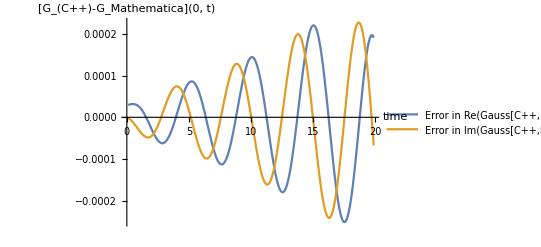

```mathematica
(DataGrep=Table[{t,Grep[coordinate,t]},{t,0.1,20,0.1}];)//AbsoluteTiming
xRe=Table[{DataGrep⟦i,1⟧,Re[DataGrep⟦i,2⟧]},{i,1, Length[DataGrep]}];
xIm=Table[{DataGrep⟦i,1⟧,Im[DataGrep⟦i,2⟧]},{i,1, Length[DataGrep]}];
figxsliceRe=ListPlot[{
Table [{xsliceRe⟦i,1⟧,xsliceRe⟦i,2⟧-xRe⟦i,2⟧},{i,1,Min[Length[xsliceRe],Length[xRe]]}],
Table [{xsliceIm⟦i,1⟧,xsliceIm⟦i,2⟧-xIm⟦i,2⟧},{i,1,Min[Length[xsliceIm],Length[xIm]]}]
},
Joined->{True,True},
PlotLegends->Placed[{
"Error in Re(Gauss[C++,M=60] - Gauss[Wolfram,M=20])",
"Error in Im(Gauss[C++,M=60] - Gauss[Wolfram,M=20])"
},Right(*Above*)],AxesLabel -> {"time","[G_(C++)-G_Mathematica]("<>ToString[coordinate]<>", t)"} ,PlotRange->{ {0,Automatic},{Automatic,Automatic}}]
```

```mathematica
(DataGrep2=Table[{x,Grep[x,10]},{x,-5,5,0.1}];)//AbsoluteTiming
tRe=Table[{DataGrep2⟦i,1⟧,Re[DataGrep2⟦i,2⟧]},{i,1, Length[DataGrep2]}];
tIm=Table[{DataGrep2⟦i,1⟧,Im[DataGrep2⟦i,2⟧]},{i,1, Length[DataGrep2]}];
```

{7.9304,Null}

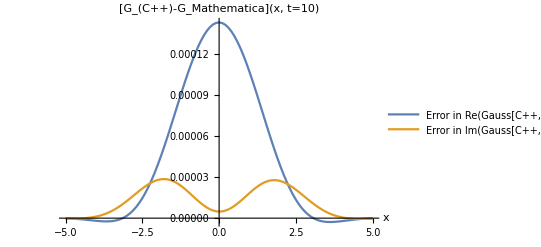

```mathematica
figtsliceRe=ListPlot[{
Table [{tsliceRe⟦i,1⟧,tsliceRe⟦i,2⟧-tRe⟦i,2⟧},{i,1,Min[Length[tsliceRe],Length[tRe]]}],
Table [{tsliceIm⟦i,1⟧,tsliceIm⟦i,2⟧-tIm⟦i,2⟧},{i,1,Min[Length[tsliceIm],Length[tIm]]}]
},
Joined->{True,True},
PlotLegends->Placed[{
"Error in Re(Gauss[C++,M=60] - Gauss[Wolfram,M=20])",
"Error in Im(Gauss[C++,M=60] - Gauss[Wolfram,M=20])"
},Right(*Above*)],AxesLabel -> {"x","[G_(C++)-G_Mathematica](x, t="<>ToString[time]<>")"} ,PlotRange->All]
```

## Slices G[x,t=10] and G[x=0, t] vs Sashas formula

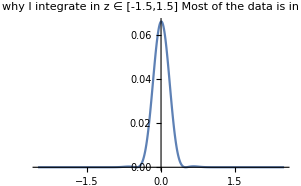

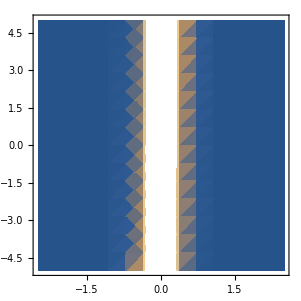

```mathematica
prerho[x_,t_,z_]=(BarnesG[1/2-z])^2/((2ⅈ (t+x))^(1/2-z)^2);
ρ[x_,t_,z_]= π Exp[-ⅈ t/2+2ⅈ x z]prerho[x,t,z]*prerho[-x,t,-z];
kF=√2 π/2.0;
EF=(kF)^2/2;

gρ[x_,t_]:= NIntegrate[ρ[kF x,EF t,z],{z,-2.5,2.5}];
T0=20.0;
X0=2.;
ListLinePlot[
Table[{z,Abs[ρ[X0,T0,z]]},{z,-2.5,2.5,0.01}]
,PlotRange->All
,PlotLabel->"That is why I integrate in z ∈ [-1.5,1.5] \n Most of the data is in this region"
]
DensityPlot[Abs[ρ[x,T0,z]],{z,-2.5,2.5},{x,-5,5}]
```

```mathematica
podgon=Abs[Grep[0.,T0]]/Abs[gρ[0.,T0]]
```

2.21118

```mathematica
(DataNum=ParallelTable[{x ,Grep[x ,T0]},{x,-5,5,0.1}];)//AbsoluteTiming
```

{5.44138,Null}

```mathematica
(DataAn2=ParallelTable[{x,gρ[x ,T0 ]},{x,-5,5,0.1}];)//AbsoluteTiming
```

{3.27992,Null}

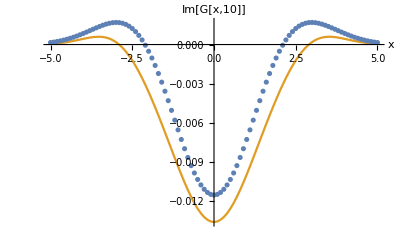

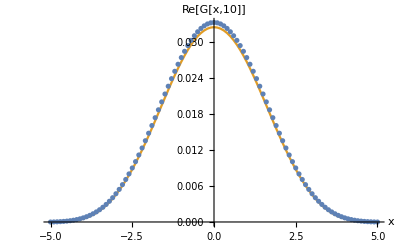

```mathematica
ListPlot[{
Table[{elem⟦1⟧,Im[elem⟦2⟧]},{elem,DataNum}],
Table[{elem⟦1⟧,podgon Im[elem⟦2⟧]},{elem,DataAn2}]
(*Table[{DataAn1⟦i,1⟧,podgon Abs[DataAn0⟦i,2⟧-DataAn1⟦i,2⟧]},{i,1,Length[DataAn1]}]*)
}
,Joined->{False,True}
,AxesLabel->{"x","Im[G[x,10]]"}
]
ListPlot[{
Table[{elem⟦1⟧,Re[elem⟦2⟧]},{elem,DataNum}],
Table[{elem⟦1⟧,podgon Re[elem⟦2⟧]},{elem,DataAn2}]
(*Table[{DataAn1⟦i,1⟧,podgon Abs[DataAn0⟦i,2⟧-DataAn1⟦i,2⟧]},{i,1,Length[DataAn1]}]*)
}
,Joined->{False,True}
,AxesLabel->{"x","Re[G[x,10]]"}
]
```

## 2D surface G[x,t]

```mathematica
(Data2D=ParallelTable[{x,t,Grep[x,t]},{x,-5,5,0.1},{t,0.1,5,0.1}];)//AbsoluteTiming
```

{876.936,Null}

```mathematica
Data2DAbs=Table[{elem⟦1⟧,elem⟦2⟧,Abs[elem⟦3⟧]},{elem,Flatten[Data2D,1]}];
Data2DRe=Table[{elem⟦1⟧,elem⟦2⟧,Re[elem⟦3⟧]},{elem,Flatten[Data2D,1]}];
Data2DIm=Table[{elem⟦1⟧,elem⟦2⟧,Im[elem⟦3⟧]},{elem,Flatten[Data2D,1]}];
Fig2dAbs=ListPlot3D[Data2DAbs
,PlotLegends->Placed[{
"|G_∞(x,t)|"
},Right(*Above*)],AxesLabel -> {"x","t"} ,PlotRange->{ {Automatic,Automatic},{Automatic,Automatic}}
]
Fig2dRe=ListPlot3D[Data2DRe
,PlotLegends->Placed[{
"Re[G_∞(x,t)]"
},Right(*Above*)],AxesLabel -> {"x","t"} ,PlotRange->{ {Automatic,Automatic},{Automatic,Automatic}}
]
Fig2dIm=ListPlot3D[Data2DIm
,PlotLegends->Placed[{
"Im[G_∞(x,t)"
},Right(*Above*)],AxesLabel -> {"x","t"} ,PlotRange->{ {Automatic,Automatic},{Automatic,Automatic}}
]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
Export["~/Programs/HardCoreBosons/Pictures_for_paper/Fig2DAbs.pdf",Fig2dAbs,"AllowRasterization"->True,ImageSize->360,ImageResolution->600];
Export["~/Programs/HardCoreBosons/Pictures_for_paper/Fig2DRe.pdf",Fig2dRe,
"AllowRasterization"->True,ImageSize->360,ImageResolution->600];
Export["~/Programs/HardCoreBosons/Pictures_for_paper/Fig2DIm.pdf",Fig2dIm,
"AllowRasterization"->True,ImageSize->360,ImageResolution->600];
```

```mathematica
Export["~/Dropbox/LPTMS/Zvonarev/Data/2D.m",Data2D]
```

~/Dropbox/LPTMS/Zvonarev/Data/2D.m

```mathematica
A=Import["~/Dropbox/LPTMS/Zvonarev/Data/2D.m"];
```

```mathematica
Table[{elem⟦1⟧,elem⟦2⟧,Abs[elem⟦3⟧]},{elem,Flatten[A,1]}]//ListPlot3D
```

-Graphics3D-

## G(p,t)=∫G(x,t)e^ⅈxp ⅆx G(p=0,t)

```mathematica
<<NumericalDifferentialEquationAnalysis`
a=4;
GaussIntegration=N[GaussianQuadratureWeights[40,-a,a]];
```

```mathematica
(Data2=ParallelTable[{x,Grep[x,0.1]},{x,-a,a,0.01}];)//AbsoluteTiming
DataRe=Table[{Data2⟦i,1⟧,Re[Data2⟦i,2⟧]},{i,1,Length[Data2]}];
DataIm=Table[{Data2⟦i,1⟧,Im[Data2⟦i,2⟧]},{i,1,Length[Data2]}];
DataAbs=Table[{Data2⟦i,1⟧,Abs[Data2⟦i,2⟧]},{i,1,Length[Data2]}];
```

{133.801,Null}

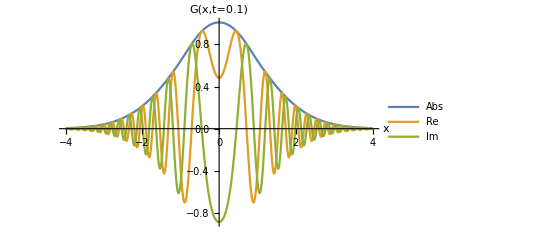

```mathematica
Fig=ListPlot[{DataAbs,DataRe,DataIm},

Joined->True,
PlotLegends->Placed[{
"Abs",
"Re",
"Im"
},Right(*Above*)],AxesLabel -> {"x","G(x,t=0.1)"} ,PlotRange->{ {Automatic,Automatic},{Automatic,Automatic}}
]
```

```mathematica
Export["~/Programs/HardCoreBosons/Pictures_for_paper/Slice_t01.pdf",Fig,
"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

~/Programs/HardCoreBosons/Pictures_for_paper/Slice_t01.pdf

```mathematica
Grep[1,1]//AbsoluteTiming
```

{2.16878,-0.0204238-0.165395 ⅈ}

```mathematica
120*0.83
```

99.6

```mathematica
(ParallelSum[Grep[x,0.1]*δx,{x,-4,4,δx}])//AbsoluteTiming
```

{132.669,0.742775-0.249382 ⅈ}

```mathematica
Exp[2.]
```

7.38906

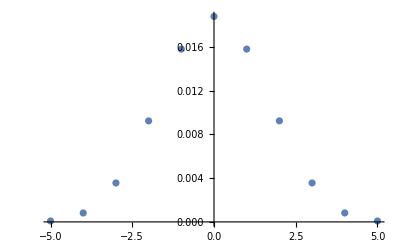

```mathematica
ListPlot[ParallelTable[{x,Im[Grep[x,Exp[3.9]]]},{x,-5,5,1.}]]
```

```mathematica
δx=0.1;
(GptData=Table[{N[Exp[τ]],ParallelSum[Grep[x,N[Exp[τ]]]*δx,{x,-5,5,δx}]},{τ,2.9,3.9,0.1}])//AbsoluteTiming
```

{263.96,{{6.68589,-0.199098-0.108441 ⅈ},{7.38906,-0.201212+0.077949 ⅈ},{8.16617,-0.0493677+0.199336 ⅈ},{9.02501,0.142283+0.133961 ⅈ},{9.97418,0.170255-0.0747174 ⅈ},{11.0232,-0.0235775-0.175254 ⅈ},{12.1825,-0.168117-0.00188056 ⅈ},{13.4637,-0.00110653+0.159817 ⅈ},{14.8797,0.149895-0.0245636 ⅈ},{16.4446,-0.0709851-0.12564 ⅈ},{18.1741,-0.0660678+0.120069 ⅈ}}}

```mathematica
GaussIntegration=N[GaussianQuadratureWeights[20,-5,5]];
(GptData=Table[{N[Exp[τ]],ParallelSum[Grep[x⟦1⟧,N[Exp[τ]]]*x⟦2⟧,{x,GaussIntegration}]},{τ,1.9,1.9,0.1}])//AbsoluteTiming
```

{21.7899,{{6.68589,-0.199102-0.108463 ⅈ}}}

```mathematica
Exp[3.9]
```

49.4024

```mathematica
GpTotal=GptData;
```

```mathematica
AppendTo[GpTotal,GptData]
```

{{0.00673795,0.93559-0.0649414 ⅈ},{0.0183156,0.892017-0.107432 ⅈ},{0.0497871,0.820932-0.176725 ⅈ},{0.135335,0.697994-0.289157 ⅈ},{0.367879,0.458252-0.454797 ⅈ},{{1.,-0.070641-0.505368 ⅈ},{2.71828,-0.231459+0.257647 ⅈ},{7.38906,-0.201156+0.07795 ⅈ}}}

```mathematica
GpTotal={
{0.0009118819655545162,0.9759729907936859-0.023987979932444795 ⅈ},{0.0010077854290485105,0.9747419639404983-0.02525562592071627 ⅈ},
{0.0011137751478448024,0.9734439178041238-0.026549663420723884 ⅈ},{0.001230911902673481,0.9720820262677659-0.02791145051382207 ⅈ},
{0.0013603680375478928,0.9706477087801778-0.02934280960851076 ⅈ},{0.0015034391929775724,0.9691451005732608-0.03084729406816827 ⅈ},
{0.001661557273173934,0.9675619208071238-0.032428386444903125 ⅈ},{0.0018363047770289056,0.9658976963305694-0.034090678867108655 ⅈ},
{0.002029430636295734,0.9641498354414562-0.03583888871120552 ⅈ},{0.002242867719485801,0.962310056597881-0.03767911254497803 ⅈ},
{0.0024787521766663585,0.9603758828887355-0.03960836282707948 ⅈ},
{0.0027394448187683684,0.9583452992248795-0.041638513811447404 ⅈ},{0.0030275547453758127,0.9562075115671942-0.0437739303327749 ⅈ},
{0.003345965457471272,0.9539582150679468-0.04601363308895128 ⅈ},{0.003697863716482929,0.9515963930522735-0.048375938056086476 ⅈ},
{0.004086771438464067,0.9491104716833884-0.0508528243992719 ⅈ},{0.004516580942612666,0.9465020530993302-0.05345598742547786 ⅈ},
{0.004991593906910213,0.9437548508250755-0.056194730672992 ⅈ},{0.0055165644207607716,0.940866359362395-0.059074072253969295 ⅈ},
{0.006096746565515633,0.9378341088459964-0.06210286492022932 ⅈ},{0.006737946999085467,0.9355899777947948-0.06494136473258834 ⅈ},
{0.007446583070924338,0.9312828329715721-0.06863047692467428 ⅈ},{0.008229747049020023,0.9277479044359795-0.07214091568419725 ⅈ},
{0.009095277101695816,0.9240347368047048-0.07583497632172628 ⅈ},{0.010051835744633576,0.920129135537555-0.07972156848023242 ⅈ},
{0.011108996538242306,0.9160245134025857-0.08380473202737247 ⅈ},{0.012277339903068436,0.9117029516685908-0.08809411290909938 ⅈ},
{0.013568559012200922,0.9071588217015831-0.09259469374604744 ⅈ},{0.014995576820477703,0.9023762968479402-0.0973327202261777 ⅈ},
{0.016572675401761237,0.8973455875272741-0.10231989053986477 ⅈ},{0.01831563888873418,0.8920171636494725-0.10743168670125475 ⅈ},
{0.02024191144580439,0.8864869953845782-0.11304937988545066 ⅈ},{0.0223707718561656,0.8806141695559238-0.1188271072260402 ⅈ},
{0.0247235264703394,0.8744501196443555-0.12489296080810566 ⅈ},{0.02732372244729257,0.8679405026987915-0.13127287732880938 ⅈ},
{0.0301973834223185,0.8610941221332091-0.13797682701610808 ⅈ},{0.03337326996032608,0.8538888039518724-0.14501022652152273 ⅈ},
{0.036883167401240015,0.8462827344230508-0.15241396752438552 ⅈ},{0.040762203978366225,0.8382716294019279-0.16017527486561184 ⅈ},
{0.04504920239355782,0.8298314115701044-0.16834190741931193 ⅈ},{0.049787068367863944,0.820932241176141-0.17672518177800012 ⅈ},{0.05502322005640723,0.8115140396442062-0.18589712155453073 ⅈ},{0.06081006262521797,0.8015674009555314-0.1953215251936772 ⅈ},
{0.06720551273974978,0.7910724097873829-0.2052206529777592 ⅈ},{0.0742735782143339,0.7799589072436544-0.2156140618043385 ⅈ},
{0.0820849986238988,0.7682194743226765-0.2265169710465254 ⅈ},{0.09071795328941251,0.7557476084161712-0.2379327275542473 ⅈ},
{0.10025884372280375,0.7425354430435519-0.24988803573111631 ⅈ},{0.11080315836233391,0.7285073226928312-0.262417477175637 ⅈ},
{0.12245642825298195,0.7136071971802924-0.275519695414807 ⅈ},{0.1353352832366127,0.6979935223202667-0.2891565228635671 ⅈ},{0.14956861922263506,0.6807767772640837-0.30349215026009435 ⅈ},{0.16529888822158656,0.6626470648888727-0.3183811414712121 ⅈ},
{0.18268352405273466,0.6432512348808528-0.33384948043172924 ⅈ},{0.20189651799465544,0.6224457089020317-0.3499029157242942 ⅈ},
{0.22313016014842982,0.6000698461529765-0.36651068783609686 ⅈ},{0.2465969639416065,0.5759586863800948-0.383620032695779 ⅈ},
{0.27253179303401265,0.5499262214455455-0.40113228397524864 ⅈ},{0.3011942119122022,0.5217126630435851-0.4189167252960385 ⅈ},
{0.3328710836980796,0.49106634082897277-0.4368893396777843 ⅈ},{0.36787944117144233,0.4582519426413507-0.45479666950809494 ⅈ},
{0.4065696597405991,0.4215291272357835-0.4722841575322406 ⅈ},{0.44932896411722156,0.3820573642438384-0.48908789388529084 ⅈ},
{0.4965853037914095,0.3389542523193604-0.5046276763743605 ⅈ},{0.5488116360940264,0.29210776475284217-0.5183095486041384 ⅈ},
{0.6065306597126334,0.24115859266973494-0.5294003370540514 ⅈ},{0.6703200460356393,0.18606091556788498-0.5368218401685703 ⅈ},
{0.7408182206817179,0.12691230852378932-0.5395451146553525 ⅈ},{0.8187307530779819,0.06389390629595967-0.5362435730388213 ⅈ},
{0.9048374180359596,-0.0023629908735495727-0.5253471654056785 ⅈ},
{1.,-0.07064096860712492-0.5053682510699686 ⅈ},{1.1051709180756477,-0.1396938536917411-0.47457559471592253 ⅈ},{1.2214027581601699,-0.20705848705649899-0.4317071782509393 ⅈ},{1.3498588075760032,-0.26991703541610856-0.3755745035090634 ⅈ},{1.4918246976412703,-0.32461251095403154-0.3056949385943326 ⅈ},{1.6487212707001282,-0.3668101823899967-0.22256534491605268 ⅈ},{1.8221188003905089,-0.39170964124534396-0.12804894334596595 ⅈ},{2.0137527074704766,-0.3943865234239669-0.025743063240100183 ⅈ},{2.225540928492468,-0.3703000439666211+0.0786113379425547 ⅈ},{2.45960311115695,-0.3161624843979952+0.17673462081798558 ⅈ},{2.718281828459045,-0.231459433002198+0.25764687756199767 ⅈ},{3.0041660239464334,-0.11968856296037769+0.30855176494027137 ⅈ},{3.320116922736548,0.008783487967681853+0.31598883688975826 ⅈ},{3.6692966676192444,0.1355320424721228+0.2697134035902586 ⅈ},{4.055199966844675,0.2340608733551761+0.16807622606026154 ⅈ},{4.4816890703380645,0.27384369883728626+0.024979419087632473 ⅈ},{4.953032424395115,0.23072625338426467-0.1247054442615004 ⅈ},{5.473947391727201,0.10385453464582012-0.22739596563153913 ⅈ},{6.049647464412947,-0.06696359799522955-0.22851973135712245 ⅈ},{6.68589444227927,-0.19909768044814397-0.10844102029392036 ⅈ},
{7.38905609893065,-0.2011559131915756+0.07794998720067953 ⅈ},{8.166169912567652,-0.049367705503706595+0.19933606262732412 ⅈ},{9.025013499434122,0.14228269062417803+0.13396147148923027 ⅈ},{9.974182454814718,0.1702549129397511-0.07471737613377376 ⅈ},{11.023176380641601,-0.023577460257119168-0.17525374445333966 ⅈ},{12.182493960703473,-0.16811661851087592-0.0018805557717095417 ⅈ},{13.463738035001692,-0.0011065338703951611+0.15981714387357693 ⅈ},{14.879731724872837,0.14989462046848706-0.024563561619103377 ⅈ},{16.444646771097048,-0.07098512702306972-0.12563968476067816 ⅈ},{18.17414536944306,-0.0660677806356669+0.12006896578291984 ⅈ},
{20.085536923187668,0.12527775170226957-0.03511627808489871 ⅈ},{22.197951281441636,-0.11882566170920009-0.03346862029366586 ⅈ},{24.532530197109352,0.0998044848691321+0.06118583651505605 ⅈ},{27.112638920657883,-0.09604172502838587-0.055524210227810414 ⅈ},{29.96410004739701,0.10360629020151155+0.017305449592429193 ⅈ},{33.11545195869231,-0.08412164832363024+0.05287864457854512 ⅈ},{36.59823444367799,-0.011596909887429717-0.09315921806532097 ⅈ},{40.4473043600674,0.08775442458824545-0.012023051326039437 ⅈ},{44.701184493300815,0.05019386667302515+0.06664411429422504 ⅈ},{49.40244910553017,0.010442774134765607+0.07773666719103547 ⅈ},{54.598150033144236,0.016545550868461725+0.07171488544254155 ⅈ}
};
```

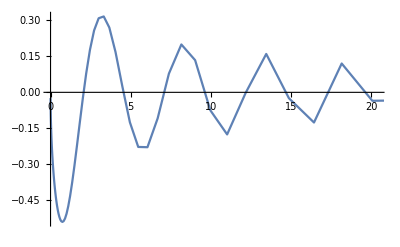

Function[{η,x,t,Gauss},Block[{ϵ=1/10^6,p=Table[elem⟦1⟧,{elem,Gauss}],τ=t p^2 0.5-x p,τϵ=t (p+ϵ)^2 0.5-x (p+ϵ),θ=1./(Exp[100. (p^2 0.5-0.5 (π 0.5)^2)]+1.),Emin=√(θ/π) Exp[ⅈ τ 0.5],EinftyW=Table[Exp[-ⅈ τ⟦i⟧] (Sin[η 0.5] ⅈ Erf[((x-Gauss⟦i,1⟧ t) (1.-ⅈ))/(2 √t)]+Cos[η 0.5]),{i,1,Length[Gauss]}],EinftyWϵ=Table[Exp[-ⅈ τϵ⟦i⟧] (Sin[η 0.5] ⅈ Erf[((x-(Gauss⟦i,1⟧+ϵ) t) (1.-ⅈ))/(2 √t)]+Cos[η 0.5]),{i,1,Length[Gauss]}],detV=Det[Table[i,j+(√Gauss⟦i,2⟧ (Emin⟦i⟧ Emin⟦j⟧ Sin[η 0.5] (EinftyWϵ⟦i⟧-EinftyW⟦j⟧)) √Gauss⟦j,2⟧)/(Gauss⟦i,1⟧+ϵ-Gauss⟦j,1⟧),{i,1,Length[Gauss]},{j,1,Length[Gauss]}]],detWV=Det[Table[i,j+√Gauss⟦i,2⟧ (Emin⟦i⟧ Emin⟦j⟧ ((Sin[η 0.5] (EinftyWϵ⟦i⟧-EinftyW⟦j⟧))/(Gauss⟦i,1⟧+ϵ-Gauss⟦j,1⟧)-0.5 EinftyW⟦i⟧ EinftyW⟦j⟧)) √Gauss⟦j,2⟧,{i,1,Length[Gauss]},{j,1,Length[Gauss]}]]},(Exp[-(ⅈ π)/4.] √(1./(2. π t)) Exp[(ⅈ (x x))/(2. t)]-1) detV+detWV]]

```mathematica
Table[{elem⟦1⟧,Im[elem⟦2⟧]},{elem,GpTotal}]//ListLinePlot
```

```mathematica
Table[Log[elem⟦1⟧],{elem,GpTotal}]
ListPlot[Table[Log[elem⟦1⟧],{elem,GpTotal}]]
```

```mathematica
kF=√2(π 0.5);
EF=(kF)^2/2;
gρ[x_,t_]:=NIntegrate[ρ[kF x,EF t,z],{z,-1.5,1.5}];
```

```mathematica
Grep[0,50.]/gρ[0,50.]
```

0.828663+0.228878 ⅈ

0.828663+0.228878 ⅈ

```mathematica
GaussIntegration=N[GaussianQuadratureWeights[40,-6,6]];
DataLargeTime=Table[{N[Exp[τ]],ParallelSum[gρ[x⟦1⟧,N[Exp[τ]]]*x⟦2⟧,{x,GaussIntegration}]},{τ,1.9,4.0,0.1}];
```

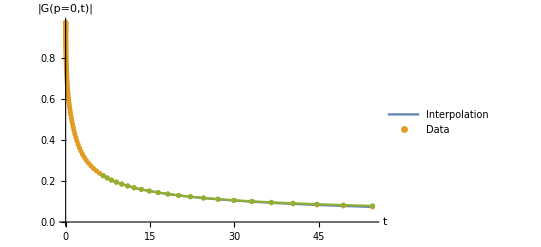

```mathematica
Fig=ListPlot[{
(*Table[{elem⟦1⟧,Re[elem⟦2⟧]},{elem,GpTotal}],
Table[{elem⟦1⟧,Im[elem⟦2⟧]},{elem,GpTotal}],*)
Table[{elem⟦1⟧,Abs[elem⟦2⟧]},{elem,GpTotal}],
Table[{elem⟦1⟧,Abs[elem⟦2⟧]},{elem,Sort[GpTotal]}],
Table[{elem⟦1⟧,0.95*Abs[elem⟦2⟧]},{elem,Sort[DataLargeTime]}]

(*,Table[{elem⟦1⟧,Re[elem⟦2⟧]},{elem,Sort[GpTotal]}]
,Table[{elem⟦1⟧,Im[elem⟦2⟧]},{elem,Sort[GpTotal]}]*)
},
Joined->{True,False},
PlotLegends->Placed[{
"Interpolation",
"Data"
},Right(*Above*)],AxesLabel -> {"t","|G(p=0,t)|"} ,PlotRange->All]
```

```mathematica
Export["~/Programs/HardCoreBosons/Pictures_for_paper/GptLogLog.pdf",Fig,
"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

~/Programs/HardCoreBosons/Pictures_for_paper/GptLogLog.pdf

```mathematica
A=ParallelTable[{t,Re[Grep[0,t]]},{t,0.1,20,0.1}];
```

```mathematica
B2=ParallelTable[{t,Re[Grep[0,t]]},{t,20,40,0.1}];
```

```mathematica
Analyt=ParallelTable[{t,Re[gρ[0,2(π 0.5)^2/2 t]]},{t,0.1,40,0.05}];
```

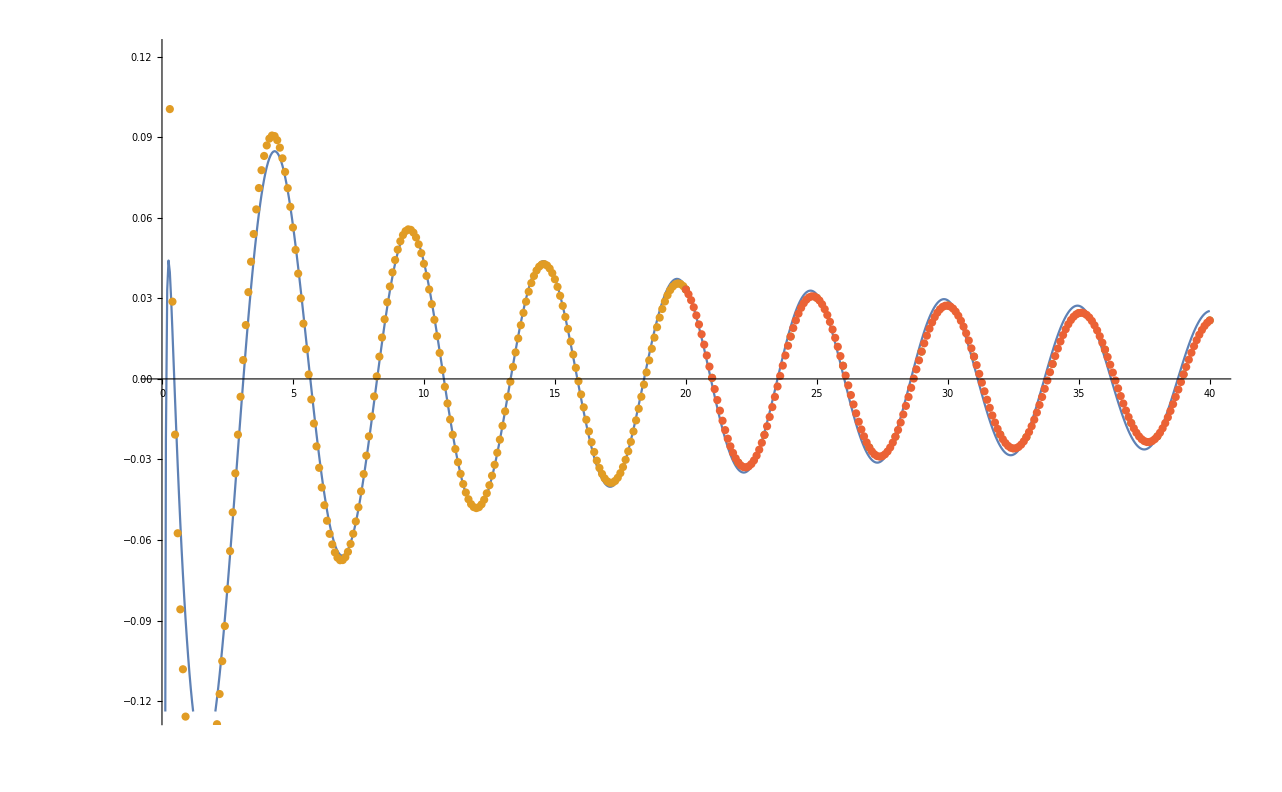

```mathematica
prerho[x_,t_,z_]=(BarnesG[1/2-z])^2/((2ⅈ (t+x))^((1/2-z))^2);
ρ[x_,t_,z_]= 2.3167217952824637*π Exp[-ⅈ t/2+2ⅈ x z]prerho[x,t,z]*prerho[-x,t,-z];
gρ[x_,t_]:=NIntegrate[ρ[0,t,z],{z,-0.5,0.5}];

ListPlot[{
Analyt,
A,B,B2
}
,Joined->{True,False,False,False}
]
```

```mathematica
DataRe2=Table[{Data⟦i,1⟧,Re[Data⟦i,2⟧]},{i,1,Length[Data]}];
DataIm2=Table[{Data⟦i,1⟧,Im[Data⟦i,2⟧]},{i,1,Length[Data]}];
DataAbs2=Table[{Data⟦i,1⟧,Abs[Data⟦i,2⟧]},{i,1,Length[Data]}];
```

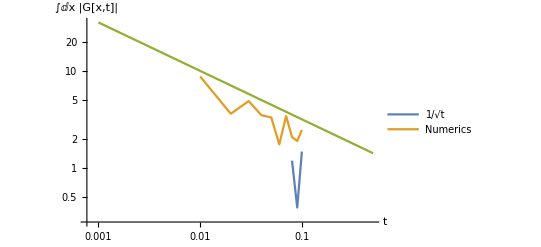

```mathematica
Fig=ListLogLogPlot[{DataRe2,DataAbs2,
Table[{x,x^(-0.5)},{x,0.001,0.5,0.001}]
},

Joined->True,
PlotLegends->Placed[{
"1/√t",
"Numerics"
},Right(*Above*)],AxesLabel -> {"t","∫ⅆx |G[x,t]|"} ,PlotRange->{ {Automatic,Automatic},{Automatic,Automatic}}
]
```

```mathematica
Export["~/Dropbox/LPTMS/Zvonarev/Pictures/Gpt_near_0.pdf",Fig]
```

~/Dropbox/LPTMS/Zvonarev/Pictures/Gpt_near_0.pdf

## 2D surface G[x,t]

```mathematica
(Data2D=ParallelTable[{x,t,Grep[x,t]},{x,-5,5,0.1},{t,0.1,5,0.1}];)//AbsoluteTiming
```

{876.936,Null}

```mathematica
Data2DAbs=Table[{elem⟦1⟧,elem⟦2⟧,Abs[elem⟦3⟧]},{elem,Flatten[Data2D,1]}];
Data2DRe=Table[{elem⟦1⟧,elem⟦2⟧,Re[elem⟦3⟧]},{elem,Flatten[Data2D,1]}];
Data2DIm=Table[{elem⟦1⟧,elem⟦2⟧,Im[elem⟦3⟧]},{elem,Flatten[Data2D,1]}];
Fig2dAbs=ListPlot3D[Data2DAbs
,PlotLegends->Placed[{
"|G_∞(x,t)|"
},Right(*Above*)],AxesLabel -> {"x","t"} ,PlotRange->{ {Automatic,Automatic},{Automatic,Automatic}}
]
Fig2dRe=ListPlot3D[Data2DRe
,PlotLegends->Placed[{
"Re[G_∞(x,t)]"
},Right(*Above*)],AxesLabel -> {"x","t"} ,PlotRange->{ {Automatic,Automatic},{Automatic,Automatic}}
]
Fig2dIm=ListPlot3D[Data2DIm
,PlotLegends->Placed[{
"Im[G_∞(x,t)"
},Right(*Above*)],AxesLabel -> {"x","t"} ,PlotRange->{ {Automatic,Automatic},{Automatic,Automatic}}
]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
Export["~/Programs/HardCoreBosons/Pictures_for_paper/Fig2DAbs.pdf",Fig2dAbs,"AllowRasterization"->True,ImageSize->360,ImageResolution->600];
Export["~/Programs/HardCoreBosons/Pictures_for_paper/Fig2DRe.pdf",Fig2dRe,
"AllowRasterization"->True,ImageSize->360,ImageResolution->600];
Export["~/Programs/HardCoreBosons/Pictures_for_paper/Fig2DIm.pdf",Fig2dIm,
"AllowRasterization"->True,ImageSize->360,ImageResolution->600];
```

```mathematica
Export["~/Dropbox/LPTMS/Zvonarev/Data/2D.m",Data2D]
```

~/Dropbox/LPTMS/Zvonarev/Data/2D.m

```mathematica
A=Import["~/Dropbox/LPTMS/Zvonarev/Data/2D.m"];
```

```mathematica
Table[{elem⟦1⟧,elem⟦2⟧,Abs[elem⟦3⟧]},{elem,Flatten[A,1]}]//ListPlot3D
```

-Graphics3D-

## Fourier G[x,t]

### 1D Fourier for Sin[αx]

{0.014167,Null}

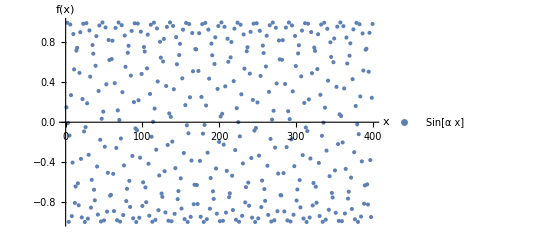

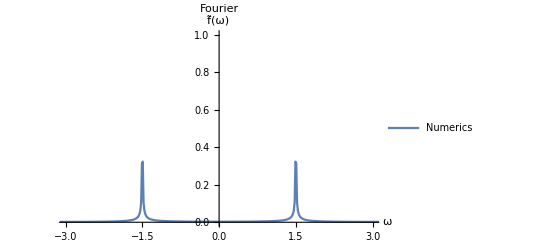

```mathematica
T=400;
T0=0.1;
dt=1;
Period=T-T0;
(Data=ParallelTable[Sin[1.5t],{t,T0,T,dt}];)//AbsoluteTiming

FData=Fourier[Data,FourierParameters->{-1,1}]; FData=RotateRight[FData,Floor[Length[FData]/2]];

ListPlot[
{
Table[{(j*dt),Re[Data⟦j⟧]},{j,1,Length[Data]}]
}
,Joined->{False}
(*,PlotLabel->"Original Data"*)
,PlotLegends->Placed[{"Sin[α x]"},Right(*Above*)]
,AxesLabel -> {"x","f(x)"} ,PlotRange->{ {Automatic,Automatic},{Automatic,Automatic}}
]
ListPlot[{
Table[{(j-1-Floor[Length[FData]/2])*((2π)/Period),Abs[FData⟦j⟧]},{j,1,Length[FData]}]
}
,Joined->{True}
,PlotStyle->PointSize[0.01]
,PlotLabel->"Fourier"
,PlotLegends->Placed[{
"Numerics"
},Right(*Above*)]
,AxesLabel -> {"ω","f̃(ω)"} ,PlotRange->{{-3,3},{0,1}}
]
```

### 2D Fourier for Sin[αx]Sin[βy]

{0.073284,Null}

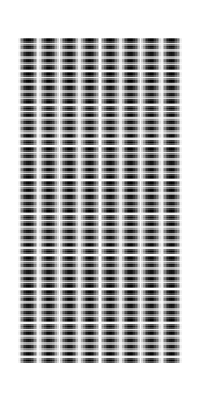

```mathematica
T=20;
T0=0;
dt=0.1;
PeriodT=T-T0;

X1=5;
X0=-5;
dx=0.1;
PeriodX=T-T0;

(Data=ParallelTable[Sin[7.5t]Sin[2.5x],{t,T0,T,dt},{x,X0,X1,dx}];)//AbsoluteTiming

FData=Fourier[Data,FourierParameters->{-1,1}];
For[i=1,i≤Length[FData],++i,
FData⟦i⟧=RotateRight[FData⟦i⟧,Floor[Length[FData⟦i⟧]/2]]
]
FData=RotateRight[FData,Floor[Length[FData]/2]];

ArrayPlot[Data]
```

```mathematica
OutputData=Table[{(j-1.-Floor[(T-T0)/(2dt)])*((2π)/PeriodT),
(k-1.-Floor[(X1-X0)/(2dx)])*((2π)/PeriodX),
Abs[FData⟦j,k⟧]}
,{j,Floor[(T-T0)/(2dt)],(T-T0)/dt}
,{k,(X1-X0)/(2dx),(X1-X0)/dx}];
```

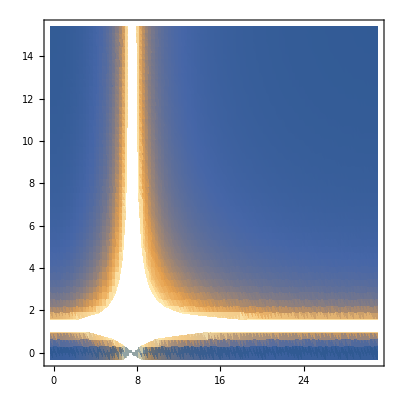

```mathematica
ListDensityPlot[
Flatten[OutputData,1]
]
```

```mathematica
FData⟦201,101⟧
```

-6.69078×10^-8-1.65038×10^-9 ⅈ

```mathematica
Animate[ListPlot[
Table[{(j-1-Floor[Length[FData]/2])*((2π)/Period),Abs[FData⟦Floor[a],j⟧]},{j,1,Length[FData]}]
,PlotRange->{{-3,3},{0,0.1}}
],{a,1,Length[FData]},AnimationRunning->False]
```

### Fourier

```mathematica
T=40;
T0=0.1;
dt=0.2;
(Data=ParallelTable[Grep[0,t],{t,T0,T,dt}];)//AbsoluteTiming
Period=T-T0;
```

{52.2651,Null}

```mathematica
(DataSasha=ParallelTable[{t,2.36gρ[0,t]},{t,T0,T,dt}];)//AbsoluteTiming
```

{1.73625,Null}

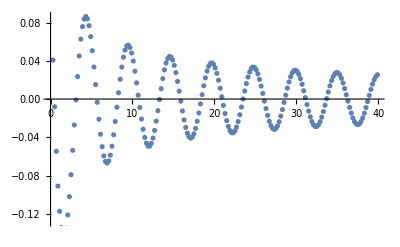

```mathematica
Table[{elem⟦1⟧,Re[elem⟦2⟧]},{elem,DataSasha}]//ListPlot
```

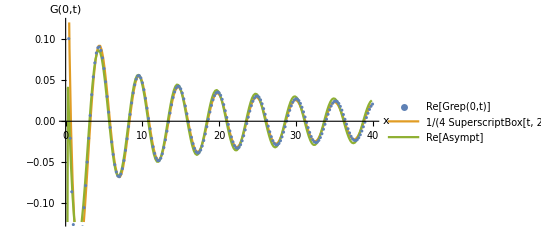

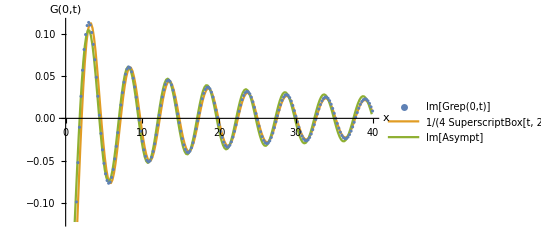

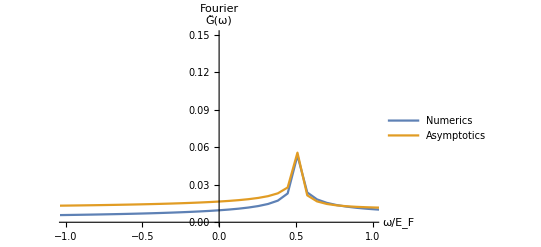

```mathematica
(*UnitBox[x]*)
kF=√2 π/2.0;
EF=(kF)^2/2;
(*
FData=Fourier[Data,FourierParameters->{-1,1}];
FData=RotateRight[FData,Floor[Length[FData]/2]];
*)
FData=Fourier[Data,FourierParameters->{-1,1}];
FData=RotateRight[FData,Floor[Length[FData]/2]];
FDataSasha=Fourier[Table[elem⟦2⟧,{elem,DataSasha}],FourierParameters->{-1,1}];
FDataSasha=RotateRight[FDataSasha,Floor[Length[FDataSasha]/2]];

FigData=ListPlot[
{
Table[{(j*dt),Re[Data⟦j⟧]},{j,1,Length[Data]}]
,Table[{t,0.25/t^(2/3)Sin[0.5*EF t+2.3]},{t,T0,T,dt}]
,Table[{elem⟦1⟧,Re[elem⟦2⟧]},{elem,DataSasha}]
}
,Joined->{False,True,True}
(*,PlotLabel->"Original Data"*)
,PlotLegends->Placed[{
"Re[Grep(0,t)]"
,"1/(4 SuperscriptBox[t, 2/3])Sin(E_F/2 t + ϕ)"
,"Re[Asympt]"
},Right(*Above*)]
,AxesLabel -> {"x","G(0,t)"} ,PlotRange->{ {Automatic,Automatic},{Automatic,Automatic}}
]

ListPlot[
{
Table[{(j*dt),Im[Data⟦j⟧]},{j,1,Length[Data]}]
,Table[{t,0.25/t^(2/3)Sin[0.5*EF t-π/2-1.0]},{t,T0,T,dt}]
,Table[{elem⟦1⟧,Im[elem⟦2⟧]},{elem,DataSasha}]
}
,Joined->{False,True,True}
(*,PlotLabel->"Original Data"*)
,PlotLegends->Placed[{
"Im[Grep(0,t)]"
,"1/(4 SuperscriptBox[t, 2/3])Sin(E_F/2 t + ϕ)"
,"Im[Asympt]"
},Right(*Above*)]
,AxesLabel -> {"x","G(0,t)"} ,PlotRange->{ {Automatic,Automatic},{Automatic,Automatic}}
]


FigFourier=ListPlot[{
Table[{(j-1-Floor[Length[FData]/2])/(EF Period/(2π)),Abs[FData⟦j⟧]},{j,1,Length[FData]}]
,Table[{(j-1-Floor[Length[FDataSasha]/2])/(EF Period/(2π)),Abs[FDataSasha⟦j⟧]},{j,1,Length[FDataSasha]}]

}
,Joined->{True,True}
,PlotStyle->PointSize[0.01]
,PlotLabel->"Fourier"
,PlotLegends->Placed[{
"Numerics"
,"Asymptotics"
},Right(*Above*)]
,AxesLabel -> {"ω/E_F","G̃(ω)"} ,PlotRange->{ {-1,1},{Automatic,0.15}}
]
```

```mathematica
Export["~/Programs/HardCoreBosons/Pictures_for_paper/FigData.pdf",FigData,
"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

~/Programs/HardCoreBosons/Pictures_for_paper/FigData.pdf

```mathematica
Export["~/Programs/HardCoreBosons/Pictures_for_paper/FigFourier.pdf",FigFourier,
"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

~/Programs/HardCoreBosons/Pictures_for_paper/FigFourier.pdf

### 2D Grep

```mathematica
T0=0.1; T1=20.;
X0=-6.; X1=6.;
PeriodT=T1-T0; PeriodX=X1-X0;
dt=0.1;
dx=0.1;
(T1-T0)/dt
(X1-X0)/dx

(Data2D=ParallelTable[{t,x,Grep[x,t]},{t,T0,T1,dt},{x,X0,X1,dx}];)//AbsoluteTiming
```

199.

120.

{126.146,Null}

```mathematica
SetDirectory[NotebookDirectory[]];
Export["2D.m",Data2D]
```

2D.m

/home/kbidzhiev/Programs/HardCoreBosons/Mathematica

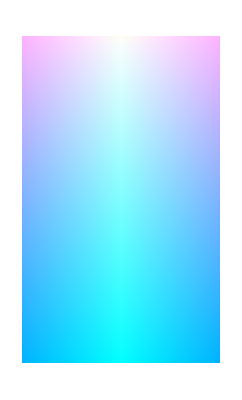

```mathematica
ArrayPlot[Abs[Data2D]]
```

### 2D Fourier for Grep

```mathematica
SetDirectory[NotebookDirectory[]];
Data2D=Import["2D.m"];
```

/home/kbidzhiev/Programs/HardCoreBosons/Mathematica

```mathematica
Data2D//Length
Data2D⟦1⟧//Length
```

200

121

```mathematica
Data2D⟦Floor[(T1-T0)/dt],Floor[(X1-X0)/dx],3⟧
```

-0.0000150942+9.05342×10^-6 ⅈ

{0.009021,Null}

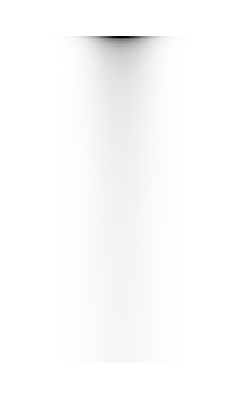
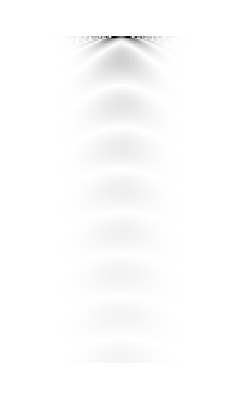
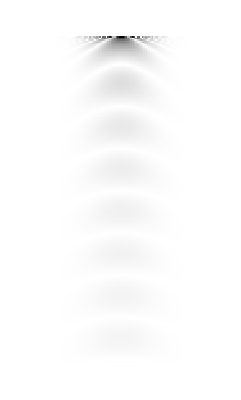

```mathematica
(Data=Table[Data2D⟦t,x,3⟧,{t,1,Floor[(T1-T0)/dt]},{x,1,Floor[(X1-X0)/dx]}];)//AbsoluteTiming

FData=Fourier[Data,FourierParameters->{-1,1}];
For[i=1,i≤Length[FData],++i,
FData⟦i⟧=RotateRight[FData⟦i⟧,Floor[Length[FData⟦i⟧]/2]]
]
FData=RotateRight[FData,Floor[Length[FData]/2]];
{ArrayPlot[Abs[Data]],ArrayPlot[Re[Data]],ArrayPlot[Im[Data]]}
```

```mathematica
kF=√2 π/2.0;
EF=(kF)^2/2;
OutputData=Table[{
(k-1.-Floor[(X1-X0)/(2dx)])*((2π)/(kF PeriodX)),
(j-1.-Floor[(T1-T0)/(2dt)])*((2π)/(EF  PeriodT)),
Abs[FData⟦j,k⟧]
}
,{j,1+Floor[(T1-T0)/(2dt)],Floor[(T1-T0)/dt]}
,{k,1+0Floor[(X1-X0)/(2dx)],Floor[(X1-X0)/dx]}];

OutputSlice=Table[{
(j-1.-Floor[(T1-T0)/(2dt)])*((2π)/(EF PeriodT)),
Im[FData⟦j,Floor[(X1-X0)/(2dx)] ⟧]
}
,{j,Floor[0.1(T1-T0)/dt],Floor[0.75(T1-T0)/dt]}];
```

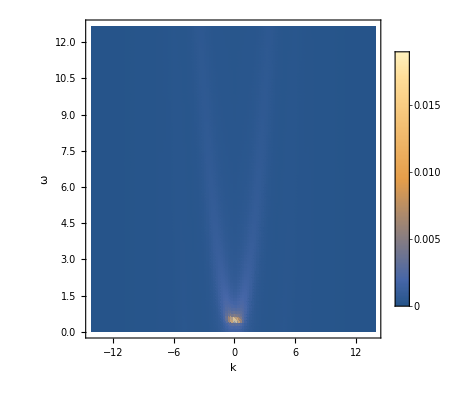

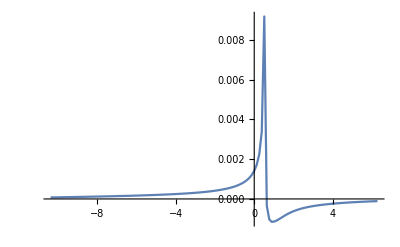

-Graphics3D-

```mathematica
ListDensityPlot[
Flatten[OutputData,1]
(*,Mesh->All*)
(*,MeshFunctions->{#3&},Mesh->5*)
,InterpolationOrder->3
(*,ClippingStyle->Automatic*)
,PlotLegends->Automatic
,PlotRange->All
,FrameLabel-> {"k","ω"} 
]

ListLinePlot[OutputSlice
,PlotRange->All
]

ListPlot3D[
Flatten[OutputData,1]
]
```

```mathematica
Animate[ListPlot[
Table[{
(k-1.-Floor[(X1-X0)/(2dx)])*((2π)/(kF PeriodX)),
(*(j-1.-Floor[(T-T0)/(2dt)])*((2π)/PeriodT),*)
Abs[Abs[FData⟦Floor[j],Floor[k]⟧]]
}
,{k,1+0(X1-X0)/(2dx),(X1-X0)/dx}
]
,Joined->{True}
,PlotRange->{{-7,7},{0,0.02}}
]
,{j,1+0(T1-T0)/(2dt),(T1-T0)/dt}
,AnimationRunning->False]
```

```mathematica
Animate[ListPlot[
Table[{
(j-1.-Floor[(T1-T0)/(2dt)])*((2π)/(EF PeriodT)),
Abs[Abs[FData⟦Floor[j],Floor[k]⟧]]
}
,{j,1+0(T1-T0)/(2dt),(T1-T0)/dt}
]
,PlotRange->{{-7,7},{0,0.021}}
]
,{k,1+0(X1-X0)/(2dx),(X1-X0)/dx}
,AnimationRunning->False]
```

6.28319

6.28319

```mathematica
PeriodX
```

20.

## Comparison with asymptotic expansion ρ(x_0,t_0,z) Eq(41) in spectralSP

Sasha has formula for ρ(x, t → ∞) :  G(x,t) = ∫ρⅆz

ρ(x,t,z) = π e^(-ⅈt/2+2ⅈxz)(G^2(1/2-z)G^2(1/2+z))/((2ⅈ(t-x))^((1/2+z)^2)(2ⅈ(t+x))^((1/2-z)^2))
We compare it with Numerics:
*in the file name ?????_# .dat,  # means fixed x value in G(x,t)

```mathematica
raynumdata=Import["~/Programs/HardCoreBosons/Data/Eta_curve1.dat"];

ρnumRe = {#[[1]],#[[2]]}&/@raynumdata;
ρnumIm = {#[[1]],#[[3]]}&/@raynumdata;
ρnumAbs = {#[[1]],#[[4]]}&/@raynumdata;

prerho[x_,t_,z_]=(BarnesG[1/2-z])^2/((2ⅈ (t+x))^(1/2-z)^2);
ρ[x_,t_,z_]=2π  Exp[-ⅈ t/2+2ⅈ x z]prerho[x,t,z]*prerho[-x,t,-z];
ray=0.5;
kF=(π 0.5);
EF=2(kF)^2/2;
t0=10;
x0=5;
```

Part::partw: Part 4 of {-3.14159,0.0843182,-0.0442995} does not exist.

Part::partw: Part 4 of {-3.13159,0.0854861,-0.0422223} does not exist.

Part::partw: Part 4 of {-3.12159,0.0865985,-0.040114} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

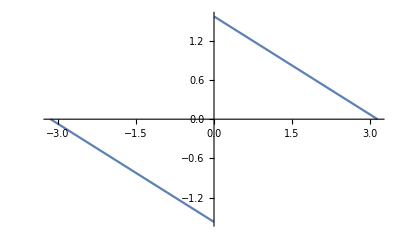

```mathematica
Plot[ArcTan[Cot[z/2]],{z,-π,π}]
```

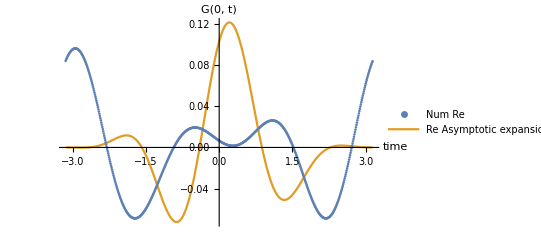

```mathematica
ρSashaRe=Table[{z ,Re[ρ[ kF x0,EF*t0,z/(2π)]]},{z,-π,π,0.01}];
figxsliceRe=ListPlot[{
(*ρnumAbs,ρSashaAbs*)
ρnumRe,ρSashaRe
},
Joined->{False,True,False,True},
PlotLegends->Placed[{
"Num Re","Re Asymptotic expansion"
,"Num Im ","Im Asymptotic expansion"
},Above],AxesLabel -> {"time","G("<>ToString[coordinate]<>", t)"}
 ,PlotRange->{{Automatic,Automatic},{Automatic,Automatic}}

]
```

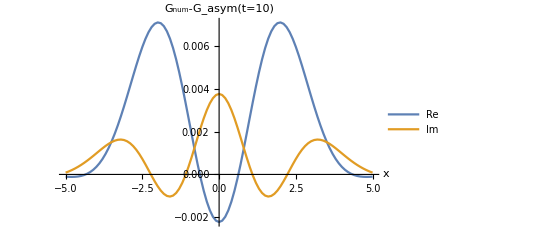

```mathematica
tSashaRe=Table[{x, Re[G[  x ,  time]]},{x,-5,5,0.01}];
tSashaIm=Table[{x, Im[G[ x,   time]]},{x,-5,5,0.01}];
figtsliceRe=ListPlot[{
Table[{tsliceRe[[k,1]], tsliceRe[[k,2]]-Re[G[ tsliceRe[[k,1]],10]]},{k,1,Length[tsliceRe]}] 
,Table[{tsliceIm[[k,1]],tsliceIm[[k,2]]-Im[G[ tsliceIm[[k,1]],10]]},{k,1,Length[tsliceIm]}] 

 },
Joined->{True,True},
PlotLegends->Placed[{
"Re","Im"
},Above],AxesLabel -> {"x","G_num-G_asym(t="<>ToString[time]<>")"}
,PlotRange->All
 ]
```

## Comparison with asymptotic expansion G(x,t)

Sasha has formula for G(x, t → ∞)
G(x,t) = (π^(3/2) G^4(1/2))/(2 √(ⅈ t)√(log(2t)+ⅈπ/2))exp(-x^2/(2(log(2t)+ⅈπ/2))-ⅈ t/2)
 (NB: G^4(1/2) → 2 BarnesG[0.5] )
We compare it with Numerics:
*in the file name xslice_# .dat,  # means fixed x value in G(x,t)

```mathematica
xslice=Import["~/Programs/HardCoreBosons/Data/xslice_0_60.dat"];
tslice=Import["~/Programs/HardCoreBosons/Data/tslice_10_60.dat"];
time =10;
coordinate = 0;
kF=√2(π 0.5);
EF=((kF)^2/2)(*-0.016*);
xsliceRe = {#[[1]],#[[2]]}&/@xslice;
xsliceIm = {#[[1]],#[[3]]}&/@xslice;

tsliceRe = {#[[1]],#[[2]]}&/@tslice;
tsliceIm = {#[[1]],#[[3]]}&/@tslice;
(*g[x_,t_]=(*1.48*)(π^(3/2) (BarnesG[0.5])^4)/(2 √(ⅈ EF t)√(Log[2EF t]+ⅈ π/(4(*2*))))Exp[-(kF x)^2/(2(Log[2EF t]+ⅈ π/(4(*2*))))-ⅈ 2(*1*)(EF t)/2];*)
prerho[x_,t_,z_]=(BarnesG[1/2-z])^2/((2ⅈ (t+x))^(1/2-z)^2);
podgon=2.3167217952824637;2.318057928747015;
podgon1=1.48630583523273;
ρ[x_,t_,z_]= podgon π Exp[-ⅈ t/2+2ⅈ x z]prerho[x,t,z]*prerho[-x,t,-z];
gρ[x_,t_]:= NIntegrate[ρ[x,t,z],{z,-1.5,1.5}];
g[x_,t_]=podgon1 (π^(3/2) (BarnesG[0.5])^4)/(2 √(ⅈ  t)√(Log[2 t]+ⅈ π/2))Exp[-( x)^2/(2(Log[2 t]+ⅈ π/2))-ⅈ t/2];
G[x_,t_]=If[t>0,g[x,t],Conjugate[g[x,t]]];
```

```mathematica
(*xSashaRe=Table[{t ,Re[G[ coordinate,t]]},{t,1,20,0.1}];*)
(*xSashaIm=Table[{t ,Im[G[ coordinate, t]]},{t,1,20,0.1}];*)
xrhoRe=Table[{t ,Re[g[kF coordinate,EF t]]},{t,1,20,0.1}];
xrhoIm=Table[{t ,Im[g[kF coordinate,EF t]]},{t,1,20,0.1}];
```

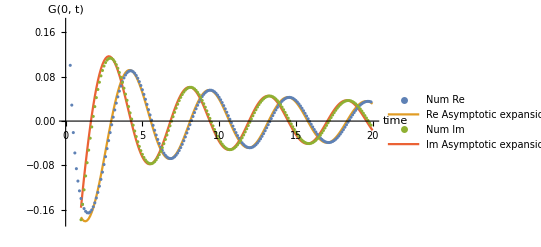

```mathematica
figxsliceRe=ListPlot[{
xsliceRe,xrhoRe
,xsliceIm,xrhoIm
},
Joined->{False,True,False,True},
PlotLegends->Placed[{
"Num Re","Re Asymptotic expansion"
,"Num Im ","Im Asymptotic expansion"
},Above],AxesLabel -> {"time","G("<>ToString[coordinate]<>", t)"} ,PlotRange->{ {0,Automatic},{Automatic,Automatic}}]
```

```mathematica
tSashaRe=Table[{x, Re[gρ[kF x,EF time]]},{x,-5,5,0.1}];
tSashaIm=Table[{x, Im[gρ[kF x,EF time]]},{x,-5,5,0.1}];
```

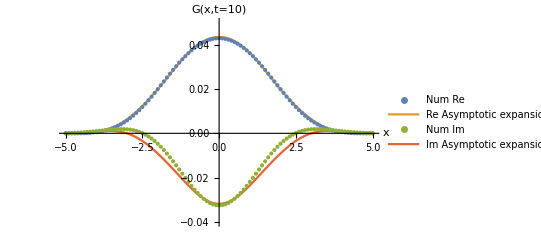

```mathematica
figtsliceRe=ListPlot[{
tsliceRe,tSashaRe 
,tsliceIm,tSashaIm
 },
Joined->{False,True,False,True},
PlotLegends->Placed[{
"Num Re","Re Asymptotic expansion"
,"Num Im ","Im Asymptotic expansion"
},Above],AxesLabel -> {"x","G(x,t="<>ToString[time]<>")"}
,PlotRange-> {{Automatic,Automatic},{-0.04,0.05}}
 ]
```

```mathematica
√(tsliceIm^2+tsliceRe^2)/Abs[gρ[0,EF time]]
√(tsliceIm^2+tsliceRe^2)/Abs[g[0,EF time]]
```

```mathematica
TableRE=Table[{tsliceRe[[k,1]], tsliceRe[[k,2]]-podgon Re[gρ[kF tsliceRe[[k,1]],EF time]]},{k,1,Length[tsliceRe],1}];
TableIM=Table[{tsliceIm[[k,1]], tsliceIm[[k,2]]-podgon Im[gρ[kF tsliceIm⟦k,1⟧,EF time  ]]},{k,1,Length[tsliceIm],1}];
```

```mathematica
TableRE2=Table[{tsliceRe[[k,1]], tsliceRe[[k,2]]-podgon Re[gρ[kF tsliceRe[[k,1]],EF time]]},{k,1,Length[tsliceRe],1}];
TableIM2=Table[{tsliceIm[[k,1]], tsliceIm[[k,2]]-podgon Im[gρ[kF tsliceIm⟦k,1⟧,EF time  ]]},{k,1,Length[tsliceIm],1}];
```

```mathematica
TableAbs=TableAbs2;
```

```mathematica
TableAbs2=Table[{tsliceIm[[k,1]],√(tsliceIm[[k,2]]^2+ tsliceRe[[k,2]]^2)- Abs[gρ[kF tsliceIm⟦k,1⟧,EF time  ]]},{k,1,Length[tsliceIm],1}];
```

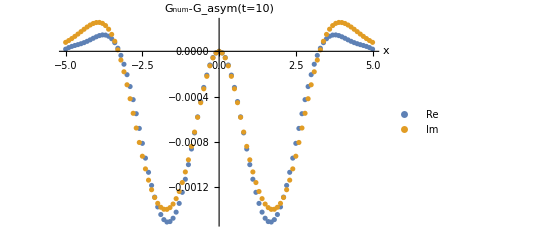

```mathematica
figtsliceRe=ListPlot[{
(* TableRE,TableIM
, TableRE2,TableIM2*)
TableAbs,TableAbs2
 },
Joined->{False,False},
PlotLegends->Placed[{
"Re","Im"
,"Re_{next order}","Im_{next order}"
},Above],AxesLabel -> {"x","G_num-G_asym(t="<>ToString[time]<>")"}
,PlotRange->All
 ]
```

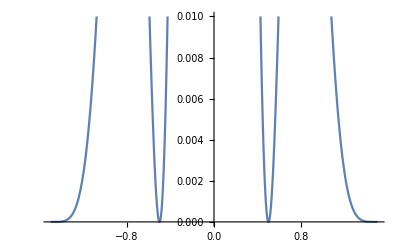

```mathematica
Plot[Abs[ρ[0,1,z]],{z,-1.5,1.5},PlotRange->{Automatic,{0,0.01}}]
```

## Comparison with asymptotic expansion ρ(x,t,z) Eq(41) in spectralSP

Sasha has formula for ρ(x, t → ∞) :  G(x,t) = ∫ρⅆz

ρ(x,t,z) = π e^(-ⅈt/2+2ⅈxz)(G^2(1/2-z)G^2(1/2+z))/((2ⅈ(t-x))^((1/2+z)^2)(2ⅈ(t+x))^((1/2-z)^2))
We compare it with Numerics:
*in the file name ?????_# .dat,  # means fixed x value in G(x,t)

```mathematica
raynumdata60=Import["~/Programs/HardCoreBosons/Data/Ray_0.5_60.dat"];
raynumdata120=Import["~/Programs/HardCoreBosons/Data/Ray_0.5_120.dat"];

ρnumRe60 = {#[[1]],#[[2]]}&/@raynumdata60;
ρnumIm60 = {#[[1]],#[[3]]}&/@raynumdata60;
ρnumAbs60 = {#[[1]],#[[4]]}&/@raynumdata60;
ρnumRe120 = {#[[1]],#[[2]]}&/@raynumdata120;
ρnumIm120 = {#[[1]],#[[3]]}&/@raynumdata120;
ρnumAbs120 = {#[[1]],#[[4]]}&/@raynumdata120;

ray=0.5;
```

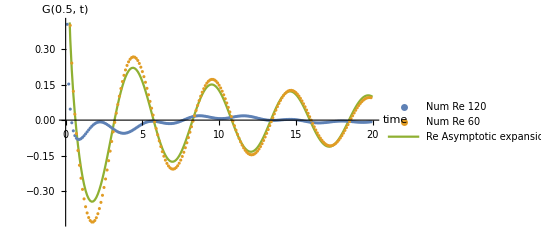

```mathematica
ρSashaRe=Table[{t ,Re[ρ[ ray*EF*t,EF*t,0]]},{t,0.1,20,0.1}];
ρSashaIm=Table[{t ,Im[ρ[ ray*EF*t, EF*t,0]]},{t,0.1,20,0.1}];
ρSashaAbs=Table[{t ,1.2Abs[ρ[ ray*EF*t, EF*t,0]]},{t,0.1,20,0.1}];
figxsliceRe=ListPlot[{
(*ρnumAbs30, ρnumAbs60,ρSashaAbs*)
ρnumRe120,ρnumRe60,ρSashaRe
(*ρnumIm120,ρnumIm60,ρSashaIm*)
},
Joined->{False,False,True},
PlotLegends->Placed[{
(*"Num 30", "Num 60", "Asymprotic"*)

"Num Re 120", "Num Re 60","Re Asymptotic expansion"
,"Num Im 120", "Num Im 60","Im Asymptotic expansion"
},Above],AxesLabel -> {"time","G("<>ToString[ray]<>", t)"}
 ,PlotRange->{{Automatic,Automatic},{Automatic,Automatic}}

]
```

```mathematica
tSashaRe=Table[{x, Re[G[  x ,  time]]},{x,-5,5,0.01}];
tSashaIm=Table[{x, Im[G[ x,   time]]},{x,-5,5,0.01}];
figtsliceRe=ListPlot[{
Table[{tsliceRe[[k,1]], tsliceRe[[k,2]]-Re[G[ tsliceRe[[k,1]],10]]},{k,1,Length[tsliceRe]}] 
,Table[{tsliceIm[[k,1]],tsliceIm[[k,2]]-Im[G[ tsliceIm[[k,1]],10]]},{k,1,Length[tsliceIm]}] 

 },
Joined->{True,True},
PlotLegends->Placed[{
"Re","Im"
},Above],AxesLabel -> {"x","G_num-G_asym(t="<>ToString[time]<>")"}
,PlotRange->All
 ]
```

-Graphics-

## Comparison RAYS ∫ρ(x,t,z) [Eq(41)] in spectralSP and G(x,t)

Sasha has formula for G(x, t → ∞)
G(x,t) = (π^(3/2) G^4(1/2))/(2 √(ⅈ t)√(log(2t)+ⅈπ/2))exp(-x^2/(2(log(2t)+ⅈπ/2))-ⅈ t/2)
 (NB: G^4(1/2) → 2 BarnesG[0.5] )
We compare it with Numerics:
*in the file name xslice_# .dat,  # means fixed x value in G(x,t)

```mathematica
raynumdata=Import["~/Programs/HardCoreBosons/Data/Ray_0.2_61.dat"];
ρnumRe = {#[[1]],#[[2]]}&/@raynumdata;
ρnumIm = {#[[1]],#[[3]]}&/@raynumdata;
ρnumAbs = {#[[1]],#[[4]]}&/@raynumdata;
ray=0.2;
kF=(π 0.5);
EF=2((kF)^2/2)(*-0.016*);

(*g[x_,t_]=(*1.48*)(π^(3/2) (BarnesG[0.5])^4)/(2 √(ⅈ EF t)√(Log[2EF t]+ⅈ π/(4(*2*))))Exp[-(kF x)^2/(2(Log[2EF t]+ⅈ π/(4(*2*))))-ⅈ 2(*1*)(EF t)/2];*)
prerho[x_,t_,z_]=(BarnesG[1/2-z])^2/((2ⅈ (t+x))^((1/2-z))^2);
ρ[x_,t_,z_]= π Exp[-ⅈ t/2+2ⅈ x z]prerho[x,t,z]*prerho[-x,t,-z];
gρ[t_]:=NIntegrate[ρ[ray t,t,z],{z,-0.5,0.5}];
g[x_,t_]=(*1.48*)(π^(3/2) (BarnesG[0.5])^4)/(2 √(ⅈ  t)√(Log[2 t]+ⅈ π/2))Exp[-(x)^2/(2(Log[2 t]+ⅈ π/2))-ⅈ t/2];
G[x_,t_]=If[t>0,g[x,t],Conjugate[g[x,t]]];
```

```mathematica
xrhoRe=Table[{t ,Re[gρ[  t]]},{t,0.1,50,1}];
(*xrhoIm=Table[{t ,Im[gρ[ t]]},{t,0.1,20,0.1}];*)
```

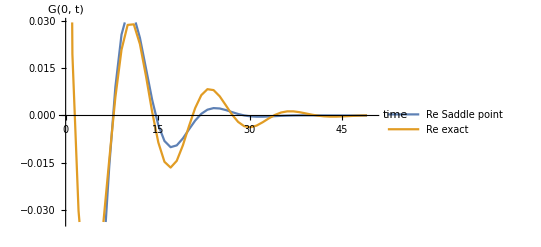

```mathematica
xSashaRe=Table[{t ,Re[G[ray t ,  t]]},{t,0.1,50,1}];
(*xSashaIm=Table[{t ,Im[G[coordinate, t]]},{t,0.1,20,0.01}];*)

figxsliceRe=ListPlot[{
xSashaRe,xrhoRe(*,ρnumRe*)
(*,xSashaIm,xrhoIm*)
},
Joined->{True,True,False},
PlotLegends->Placed[{
"Re Saddle point", "Re exact", "Re NUM"
(*,"Im Saddle point", "Im exact"*)
},Above],AxesLabel -> {"time","G("<>ToString[coordinate]<>", t)"} ,PlotRange->{ {0,50},{Automatic,Automatic}}]
```

```mathematica
|
```

```mathematica
tsliceRe[[1,2]]
```

-0.000104683

```mathematica
tSashaRe=Table[{x, Re[G[  x ,  time]]},{x,-5,5,0.01}];
tSashaIm=Table[{x, Im[G[ x,   time]]},{x,-5,5,0.01}];
figtsliceRe=ListPlot[{
Table[{tsliceRe[[k,1]], tsliceRe[[k,2]]-Re[G[ tsliceRe[[k,1]],10]]},{k,1,Length[tsliceRe]}] 
,Table[{tsliceIm[[k,1]],tsliceIm[[k,2]]-Im[G[ tsliceIm[[k,1]],10]]},{k,1,Length[tsliceIm]}] 

 },
Joined->{True,True},
PlotLegends->Placed[{
"Re","Im"
},Above],AxesLabel -> {"x","G_num-G_asym(t="<>ToString[time]<>")"}
,PlotRange->All
 ]
```

-Graphics-

```mathematica
(*xSashaIm
tSashaIm*)
tSashaRe
tsliceRe
```

```mathematica
a=1/2;
U[x_]=If[x>0,Exp[-x*x*a],0];
Φ[k_]=FourierTransform[U[x],x,k];
Φr[k_]=Re[Φ[k]];
Φi[k_]=Im[Φ[k]];
```

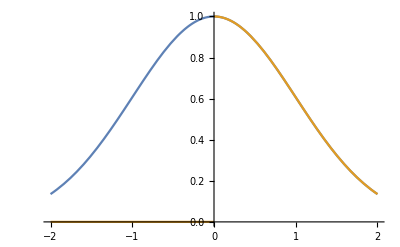

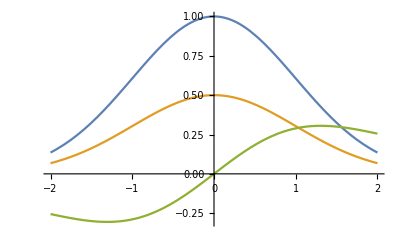

```mathematica
U0[x_]=Exp[-x*x /2];
Φ0[k_]=FourierTransform[U0[x],x,k]//Re;
Plot[{U0[x],U[x]},{x,-2,2}]
Plot[{Φ0[x],Φr[x],Φi[x]},{x,-2,2}]
```

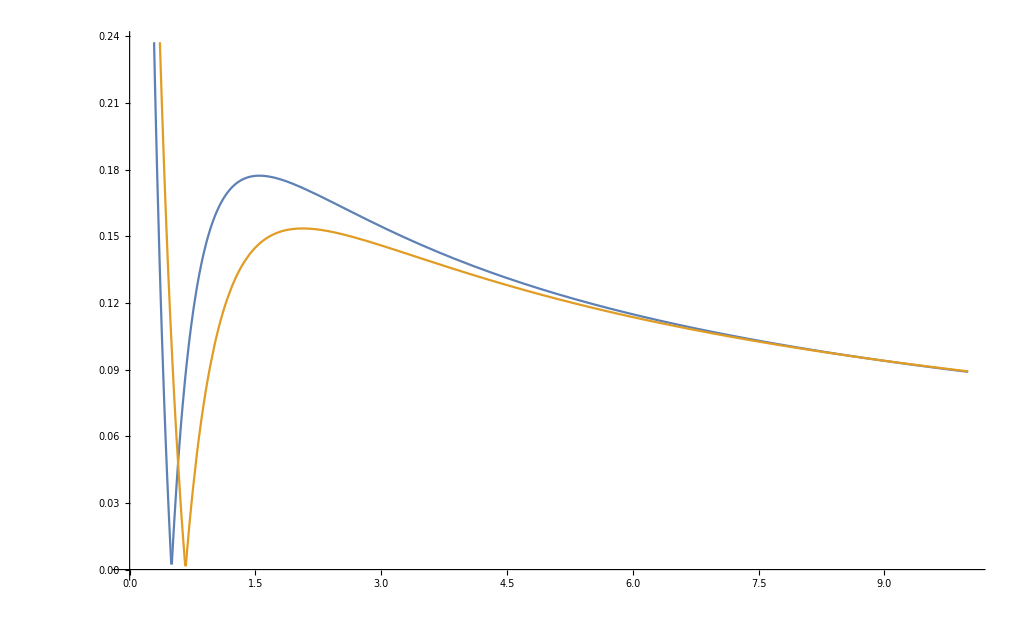

```mathematica
Plot[{Re[1/(√(ⅈ t(Log[2 t] + ⅈ π/2)))],Re[1/(√(ⅈ t(Log[1.5 t] + ⅈ π/2)))]},{t,0,10}]
```

## Comparison 2 analytics formulas, ∫ρ(x=0, t, z) [Eq(41)] in spectralSP and G(x=0,t)

Sasha has formula for G(x, t → ∞)
G(x,t) = (π^(3/2) G^4(1/2))/(2 √(ⅈ t)√(log(2t)+ⅈπ/2))exp(-x^2/(2(log(2t)+ⅈπ/2))-ⅈ t/2)
 (NB: G^4(1/2) → 2 BarnesG[0.5] )
We compare it with Numerics:
*in the file name xslice_# .dat,  # means fixed x value in G(x,t)

```mathematica
kF=(π 0.5);
EF=((kF)^2/2)(*-0.016*);

(*g[x_,t_]=(*1.48*)(π^(3/2) (BarnesG[0.5])^4)/(2 √(ⅈ EF t)√(Log[2EF t]+ⅈ π/(4(*2*))))Exp[-(kF x)^2/(2(Log[2EF t]+ⅈ π/(4(*2*))))-ⅈ 2(*1*)(EF t)/2];*)
prerho[x_,t_,z_]=(BarnesG[1/2-z])^2/((2ⅈ (t+x))^((1/2-z))^2);
ρ[x_,t_,z_]= π Exp[-ⅈ t/2+2ⅈ x z]prerho[x,t,z]*prerho[-x,t,-z];
gρ[t_]:=NIntegrate[ρ[0,t,z],{z,-0.5,0.5}];
g[x_,t_]=(*1.48*)(π^(3/2) (BarnesG[0.5])^4)/(2 √(ⅈ  t)√(Log[2 t]+ⅈ π/2))Exp[-(x)^2/(2(Log[2 t]+ⅈ π/2))-ⅈ t/2];
G[x_,t_]=If[t>0,g[x,t],Conjugate[g[x,t]]];
```

```mathematica
xrhoRe=Table[{t ,Re[gρ[EF t]]},{t,0.1,40,0.25}];
```

```mathematica
xrhoIm=Table[{t ,Im[gρ[EF t]]},{t,0.1,40,0.25}];
xSashaRe=Table[{t ,2/π Re[G[0,EF t]]},{t,0.1,40,0.25}];
xSashaIm=Table[{t ,2/π Im[G[0, EF t]]},{t,0.1,40,0.25}];
```

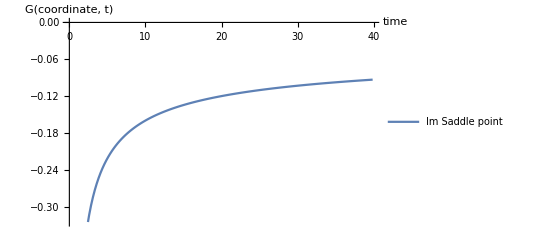

```mathematica
Diff=Table[{t ,Im[(2/π G[0, EF t]-gρ[EF t])/gρ[EF t]]},{t,0.1,40,0.25}];

figxsliceRe=ListPlot[{
Diff
(*xSashaRe,xrhoRe*)
(*xSashaIm,xrhoIm*)
},
Joined->{True,True,True,True},
PlotLegends->Placed[{
(*"Re Saddle point", "Re exact"*)
"Im Saddle point", "Im exact"
},Above],AxesLabel -> {"time","G("<>ToString[coordinate]<>", t)"} ,PlotRange->{ {Automatic,Automatic},{Automatic,Automatic}}]
```

```mathematica
|
```

```mathematica
tsliceRe[[1,2]]
```

-0.000104683

```mathematica
tSashaRe=Table[{x, Re[G[  x ,  time]]},{x,-5,5,0.01}];
tSashaIm=Table[{x, Im[G[ x,   time]]},{x,-5,5,0.01}];
figtsliceRe=ListPlot[{
Table[{tsliceRe[[k,1]], tsliceRe[[k,2]]-Re[G[ tsliceRe[[k,1]],10]]},{k,1,Length[tsliceRe]}] 
,Table[{tsliceIm[[k,1]],tsliceIm[[k,2]]-Im[G[ tsliceIm[[k,1]],10]]},{k,1,Length[tsliceIm]}] 

 },
Joined->{True,True},
PlotLegends->Placed[{
"Re","Im"
},Above],AxesLabel -> {"x","G_num-G_asym(t="<>ToString[time]<>")"}
,PlotRange->All
 ]
```

-Graphics-

```mathematica
(*xSashaIm
tSashaIm*)
tSashaRe
tsliceRe
```

```mathematica
a=1/2;
U[x_]=If[x>0,Exp[-x*x*a],0];
Φ[k_]=FourierTransform[U[x],x,k];
Φr[k_]=Re[Φ[k]];
Φi[k_]=Im[Φ[k]];
```

```mathematica
U0[x_]=Exp[-x*x /2];
Φ0[k_]=FourierTransform[U0[x],x,k]//Re;
Plot[{U0[x],U[x]},{x,-2,2}]
Plot[{Φ0[x],Φr[x],Φi[x]},{x,-2,2}]
```

-Graphics-

-Graphics-

```mathematica
Plot[{Re[1/(√(ⅈ t(Log[2 t] + ⅈ π/2)))],Re[1/(√(ⅈ t(Log[1.5 t] + ⅈ π/2)))]},{t,0,10}]
```

-Graphics-

## Comparison ∫ρ(x=0, t, z) : zϵ[-1/2:1/2] AND zϵ[-3/2:3/2]

```mathematica
prerho[x_,t_,z_]=(BarnesG[1/2-z])^2/((2ⅈ (t+x))^((1/2-z))^2);
ρ[x_,t_,z_]= π Exp[-ⅈ t/2+2ⅈ x z]prerho[x,t,z]*prerho[-x,t,-z];
gρ0[t_]:=NIntegrate[ρ[0,t,z],{z,-0.5,0.5}];
gρ1[t_]:=NIntegrate[ρ[0,t,z],{z,-1.5,1.5}];
```

```mathematica
xrhoRe0=Table[{t ,Re[gρ0[t]]},{t,0.1,40,0.25}];
xrhoRe1=Table[{t ,Re[gρ1[t]]},{t,0.1,40,0.25}];
```

```mathematica
xrhoIm0=Table[{t ,Im[gρ0[t]]},{t,0.1,40,0.25}];
xrhoIm1=Table[{t ,Im[gρ1[t]]},{t,0.1,40,0.25}];
```

```mathematica
DiffRe=Table[{t ,Re[(gρ0[t]-gρ1[t])/gρ0[t]]},{t,0.1,40,0.25}];
```

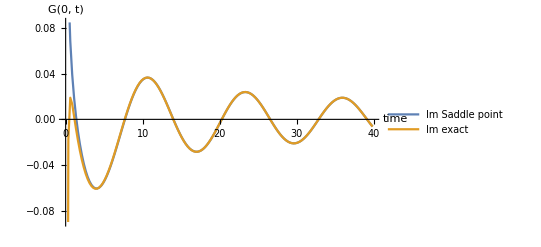

```mathematica
figxsliceRe=ListPlot[{
(*DiffRe*)
xrhoRe0,xrhoRe1
},
Joined->{True,True,True,True},
PlotLegends->Placed[{
(*"Re Saddle point", "Re exact"*)
"Im Saddle point", "Im exact"
},Above],AxesLabel -> {"time","G("<>ToString[coordinate]<>", t)"} ,PlotRange->{ {Automatic,Automatic},{Automatic,Automatic}}]
```

```mathematica
tsliceRe[[1,2]]
```

-0.000104683

```mathematica
tSashaRe=Table[{x, Re[G[  x ,  time]]},{x,-5,5,0.01}];
tSashaIm=Table[{x, Im[G[ x,   time]]},{x,-5,5,0.01}];
figtsliceRe=ListPlot[{
Table[{tsliceRe[[k,1]], tsliceRe[[k,2]]-Re[G[ tsliceRe[[k,1]],10]]},{k,1,Length[tsliceRe]}] 
,Table[{tsliceIm[[k,1]],tsliceIm[[k,2]]-Im[G[ tsliceIm[[k,1]],10]]},{k,1,Length[tsliceIm]}] 

 },
Joined->{True,True},
PlotLegends->Placed[{
"Re","Im"
},Above],AxesLabel -> {"x","G_num-G_asym(t="<>ToString[time]<>")"}
,PlotRange->All
 ]
```

-Graphics-

```mathematica
(*xSashaIm
tSashaIm*)
tSashaRe
tsliceRe
```

```mathematica
a=1/2;
U[x_]=If[x>0,Exp[-x*x*a],0];
Φ[k_]=FourierTransform[U[x],x,k];
Φr[k_]=Re[Φ[k]];
Φi[k_]=Im[Φ[k]];
```

```mathematica
U0[x_]=Exp[-x*x /2];
Φ0[k_]=FourierTransform[U0[x],x,k]//Re;
Plot[{U0[x],U[x]},{x,-2,2}]
Plot[{Φ0[x],Φr[x],Φi[x]},{x,-2,2}]
```

-Graphics-

-Graphics-

```mathematica
Plot[{Re[1/(√(ⅈ t(Log[2 t] + ⅈ π/2)))],Re[1/(√(ⅈ t(Log[1.5 t] + ⅈ π/2)))]},{t,0,10}]
```

-Graphics-

## G_rep_eta at a given ray

Sasha has formula for G(x, t → ∞)
G(x,t) = (π^(3/2) G^4(1/2))/(2 √(ⅈ t)√(log(2t)+ⅈπ/2))exp(-x^2/(2(log(2t)+ⅈπ/2))-ⅈ t/2)
 (NB: G^4(1/2) → 2 BarnesG[0.5] )
We compare it with Numerics:
*in the file name xslice_# .dat,  # means fixed x value in G(x,t)

-ArcTan[Cot[x/2]]/π

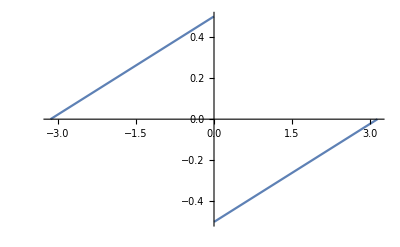

```mathematica
ArcTan[-Cot[x/2]]/π//Simplify
Plot[%,{x,-π,π}]
```

```mathematica
kF=(π 0.5);
EF=((kF)^2/2)(*-0.016*);

(*g[x_,t_]=(*1.48*)(π^(3/2) (BarnesG[0.5])^4)/(2 √(ⅈ EF t)√(Log[2EF t]+ⅈ π/(4(*2*))))Exp[-(kF x)^2/(2(Log[2EF t]+ⅈ π/(4(*2*))))-ⅈ 2(*1*)(EF t)/2];*)
prerho[x_,t_,z_]=(BarnesG[1/2-z])^2/((2ⅈ (t+x))^((1/2-z))^2);
ρ[x_,t_,z_]= π Exp[-ⅈ t/2+2ⅈ x z]prerho[x,t,z]*prerho[-x,t,-z];
gρ[t_]:=NIntegrate[ρ[0,t,z],{z,-0.5,0.5}];
g[x_,t_]=(*1.48*)(π^(3/2) (BarnesG[0.5])^4)/(2 √(ⅈ  t)√(Log[2 t]+ⅈ π/2))Exp[-(x)^2/(2(Log[2 t]+ⅈ π/2))-ⅈ t/2];
G[x_,t_]=If[t>0,g[x,t],Conjugate[g[x,t]]];
```

```mathematica
xrhoRe=Table[{t ,Re[gρ[EF t]]},{t,0.1,100,0.25}];
```

```mathematica
xrhoIm=Table[{t ,Im[gρ[EF t]]},{t,0.1,100,0.25}];
```

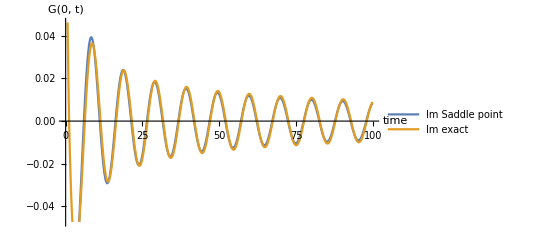

```mathematica
xSashaRe=Table[{t ,2/π Re[G[0,EF t]]},{t,0.1,100,0.25}];
xSashaIm=Table[{t ,2/π Im[G[0, EF t]]},{t,0.1,100,0.25}];

figxsliceRe=ListPlot[{
xSashaRe,xrhoRe
(*xSashaIm,xrhoIm*)
},
Joined->{True,True,True,True},
PlotLegends->Placed[{
(*"Re Saddle point", "Re exact"*)
"Im Saddle point", "Im exact"
},Above],AxesLabel -> {"time","G("<>ToString[coordinate]<>", t)"} ,PlotRange->{ {Automatic,Automatic},{Automatic,Automatic}}]
```

```mathematica
|
```

```mathematica
tsliceRe[[1,2]]
```

-0.000104683

```mathematica
tSashaRe=Table[{x, Re[G[  x ,  time]]},{x,-5,5,0.01}];
tSashaIm=Table[{x, Im[G[ x,   time]]},{x,-5,5,0.01}];
figtsliceRe=ListPlot[{
Table[{tsliceRe[[k,1]], tsliceRe[[k,2]]-Re[G[ tsliceRe[[k,1]],10]]},{k,1,Length[tsliceRe]}] 
,Table[{tsliceIm[[k,1]],tsliceIm[[k,2]]-Im[G[ tsliceIm[[k,1]],10]]},{k,1,Length[tsliceIm]}] 

 },
Joined->{True,True},
PlotLegends->Placed[{
"Re","Im"
},Above],AxesLabel -> {"x","G_num-G_asym(t="<>ToString[time]<>")"}
,PlotRange->All
 ]
```

-Graphics-

```mathematica
(*xSashaIm
tSashaIm*)
tSashaRe
tsliceRe
```

```mathematica
a=1/2;
U[x_]=If[x>0,Exp[-x*x*a],0];
Φ[k_]=FourierTransform[U[x],x,k];
Φr[k_]=Re[Φ[k]];
Φi[k_]=Im[Φ[k]];
```

```mathematica
U0[x_]=Exp[-x*x /2];
Φ0[k_]=FourierTransform[U0[x],x,k]//Re;
Plot[{U0[x],U[x]},{x,-2,2}]
Plot[{Φ0[x],Φr[x],Φi[x]},{x,-2,2}]
```

-Graphics-

-Graphics-

```mathematica
Plot[{Re[1/(√(ⅈ t(Log[2 t] + ⅈ π/2)))],Re[1/(√(ⅈ t(Log[1.5 t] + ⅈ π/2)))]},{t,0,10}]
```

-Graphics-

## MomentaSlices in 2D Fourier

```mathematica
m0=Import["~/Programs/HardCoreBosons/Data/Bckp/momentum0_fft_Gauss61.dat"];
mSasha=Import["~/Programs/HardCoreBosons/Data/momentum0_fft_Gauss41.dat"];
A0={-#[[1]],#[[2]],#[[3]],√(#[[2]]^2+#[[3]]^2)}&/@m0;
ASasha={-#[[1]](π 0.5)^2/2,#[[2]],#[[3]],√(#[[2]]^2+#[[3]]^2)}&/@mSasha;
A={#[[1]],#[[2]]}&/@A0;
ASasha={#[[1]],#[[2]]}&/@ASasha;
ALog={Log[#[[1]]],Log[#[[2]]]}&/@A0;
ALogSasha={Log[#[[1]]],Log[#[[2]]]}&/@ASasha;
FIG1=ListLinePlot[{A,ASasha},PlotRange->{{0,6},{-1,9}},AxesLabel -> {"ω / ω_F","Re[G(ω, k=0)]"}]
FIG2=ListLinePlot[{ALog,ALogSasha,Table[{x, -2x+1.5},{x,0,3,0.1}]},PlotRange->{{Automatic,3},{-4,Automatic}},
PlotLegends->Placed[{"Det","Asympototics","-2x+b"},Right],
AxesLabel -> {"log[ω / ω_F]","Log[ G(ω, k=0)]"}]
```

Import::nffil: File ~/Programs/HardCoreBosons/Data/Bckp/momentum0_fft_Gauss61.dat not found during Import.

Import::nffil: File ~/Programs/HardCoreBosons/Data/momentum0_fft_Gauss41.dat not found during Import.

-Graphics-

ListLinePlot::lpn: {{},{},{{0.,1.5},{0.1,1.3},{0.2,1.1},{0.3,0.9},{0.4,0.7},{0.5,0.5},{0.6,0.3},{0.7,0.1},«16»,{2.4,-3.3},{2.5,-3.5},{2.6,-3.7},{2.7,-3.9},{2.8,-4.1},{2.9,-4.3},{3.,-4.5}}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

ListLinePlot[{$Failed,$Failed,{{0.,1.5},{0.1,1.3},{0.2,1.1},{0.3,0.9},{0.4,0.7},{0.5,0.5},{0.6,0.3},{0.7,0.1},{0.8,-0.1},{0.9,-0.3},{1.,-0.5},{1.1,-0.7},{1.2,-0.9},{1.3,-1.1},{1.4,-1.3},{1.5,-1.5},{1.6,-1.7},{1.7,-1.9},{1.8,-2.1},{1.9,-2.3},{2.,-2.5},{2.1,-2.7},{2.2,-2.9},{2.3,-3.1},{2.4,-3.3},{2.5,-3.5},{2.6,-3.7},{2.7,-3.9},{2.8,-4.1},{2.9,-4.3},{3.,-4.5}}},PlotRange→{{Automatic,3},{-4,Automatic}},PlotLegends→Placed[{Det,Asympototics,-2x+b},Right],AxesLabel→{log[ω / ω_F],Log[ G(ω, k=0)]}]

```mathematica
Export["~/Programs/HardCoreBosons/Momentum0.pdf",FIG1]
```

~/Programs/HardCoreBosons/Momentum0.pdf

```mathematica
Export["~/Programs/HardCoreBosons/Momentum0LOG.pdf",FIG2]
```

~/Programs/HardCoreBosons/Momentum0LOG.pdf

## Determinant in C++ with eigen, so its Time = 0.016*n^2.37

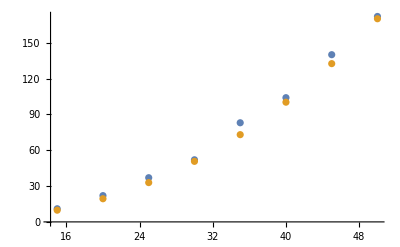

```mathematica
A={{15,11},{20,22},{25,37},{30,52},{35,83},{40,104},{45,140},{50,172}};
B=Table[{x,0.016 x^2.37},{x,15,50,5}];
ListPlot[{A,B}]
```

## Profiles for fixed k

ListLinePlot::prng: Value of option PlotRange -> {{0,10},{0,51,0,51}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

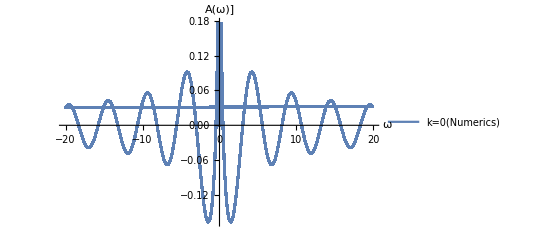

```mathematica
<<MaTeX`
(*A=Import["~/Programs/HardCoreBosons/Data/Bckp/data2d_fft_Gauss61.dat"];*)
(*A=Import["~/Programs/HardCoreBosons/Data/data2d_fft_Gauss51.dat"];*)
A=Import["~/Programs/HardCoreBosons/Data/data2d_Gauss51.dat"];

A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<4&)]; 
(*𝔸[ttime_]:=Cases[A,_?(#[[6]]==ttime&)];a[ttime_]:=𝔸[ttime][[;;,{1,2}]];(*l, Subscript[S^x, n], Subscript[S^y, n], Subscript[S^z, n], KKT, time*)
𝔹[ttime_]:=Cases[B,_?(#[[11]]==ttime&)];b[ttime_]:=𝔹[ttime][[;;,{1,8}]]*)
 (*l, Subscript[X, n] Subscript[X, n+1], Subscript[X, n] Subscript[Y, n+1], Subscript[X, n] Subscript[Z, n+1], Subscript[Y, n] Subscript[X, n+1], Subscript[Y, n] Subscript[Y, n+1], Subscript[Y, n] Subscript[Z, n+1], Subscript[Z, n] Subscript[X, n+1], Subscript[Z, n] Subscript[Y, n+1], Subscript[Z, n] Subscript[Z, n+1]*)

column =3;
momenta=0;
𝔸=Cases[A,_?(#[[1]]==momenta&)];a=𝔸[[;;,{2,column}]];

FIG=ListLinePlot[{
Table[{a[[t,1]],a[[t,2]]},{t,1,Length[a]}]
},
PlotRange -> {{0,10},{-0,51,0,51}},PlotLegends->{"k="<>ToString[momenta]<>"(Numerics)"},AxesLabel -> {"ω","A(ω)]"}]
```

```mathematica
G0[x_,t_]=Exp[-ⅈ π/4] 1/(√(2π t))Exp[ⅈ x^2/(2t)];
```

```mathematica
F[ω_,k_]=FourierTransform[HeavisideTheta[t]Exp[-ⅈ π/4] 1/(√(2π t))Exp[ⅈ x^2/(2t)],{t,x},{ω,k}];
```

```mathematica
F[ω,k]
```

-ⅈ/(π (k^2-2 ω))

```mathematica
G0[1,1.]
G0[1,-1.]
```

0.382805-0.112318 ⅈ

-0.382805-0.112318 ⅈ

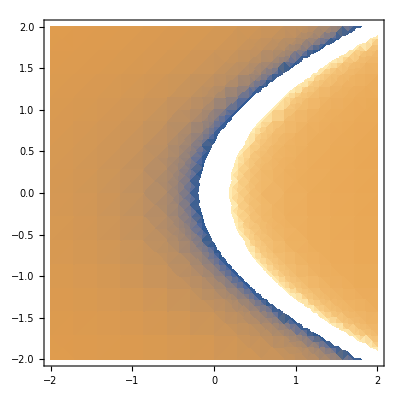

```mathematica
DensityPlot[Im[F[ω,k]],{ω,-2,2},{k,-2,2}]
```

```mathematica
Integrate[Exp[-ⅈ(t/2 (q+p)^2-x(q+p))]/q,{q,-∞,∞},PrincipalValue->True]
```

Integrate[(ⅇ^(-ⅈ (1/2 (p+q)^2 t-(p+q) x)))/q,{q,-∞,∞},PrincipalValue→True]

## F(γ, η)

```mathematica
F[γ_,η_]=1+Sum[γ^-p(Exp[ⅈ p η]+Exp[-ⅈ p η]),{p,1,∞}];
```

```mathematica
F[γ,η]//Simplify
F[2,η]//FullSimplify
G[γ_,η_]=(γ^2-1)/(γ^2+1-2γ Cos[η]);
Integrate[G[2,η],{η,-π,π}]
```

F[γ,η]

F[2,η]

2 π

```mathematica
xtest=RandomReal[];
ttest=RandomReal[];
F[1,ttest]
G[1,ttest]
```

F[1,0.73519]

0.

```mathematica
Series[G[γ,0],{γ,1,3}]
```

2/(γ-1)+1+O[γ-1]^4

```mathematica
Plot3D[Re[G[γ,η]],{γ,1,2},{η,-π,π}]
```

-Graphics3D-

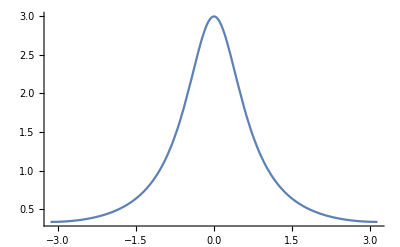

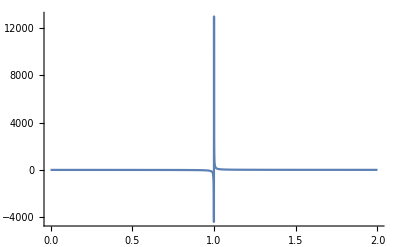

```mathematica
Plot[G[2,η],{η,-π,π},PlotRange->All]
Plot[G[γ,0],{γ,0,2},PlotRange->All]
```

## E(k) for lattice

ϵ(k)=-2Cos(k)
G(x,t)=1/(2π)∫dq e^(-ⅈt ϵ(q) + ⅈx q)=ⅈ^x J_x(2t);
 Φ(q)=e^(-ⅈt ϵ(q) + ⅈx q)
1/(2π)∫dq (Φ(q)-Φ(k))/(tan((q-k)/2))

```mathematica
ϵ[k_]=-2Cos[k];
τ[k_]:=t*ϵ[k]-x*k;
exp[k_]:=Exp[-ⅈ τ[k]];
F[q_,k_]:=1/(2π)(exp[q]-exp[k])/Tan[(q-k)/2];
Plot[{Re[F[q,0]],Im[F[q,0]]},{q,-π,π},PlotRange->All]
```

-Graphics-

```mathematica
x=5.0;
t=7.0;
Elattice[k_]:=NIntegrate[F[q,k],{q,-π,π}];
FDer[q_,k_]=D[F[q,k],k];
ElatticeDer[k_]:=NIntegrate[FDer[q,k],{q,-π,π}];

Elattice[1.14]
ElatticeDer[1.14]
```

-0.902397-0.676959 ⅈ

-3.93831+7.00175 ⅈ

```mathematica
x=2.0;
t=0.7;
√exp[1.0]
```

0.191396+0.981513 ⅈ

## G_lattice

```mathematica
1/(2π)Integrate[Exp[ⅈ(2t Cos[q]+2q)],{q,-π,π}]
B[x_,t_]=ⅈ^x BesselJ[x,2t];
```

ConditionalExpression[-BesselJ[2,2 Abs[t]],t∈ℝ]

```mathematica
Animate[
DiscretePlot[{Re[B[2x,a]],Im[B[2x,a]]},{x,-15,15},PlotRange->{{Automatic,Automatic},{-0.5,1}}, Joined->True]
,{a,0,15},AnimationRunning->False]
```

## Diagonal elements

```mathematica
t=5.0;
x=5.0;

ϵ[k_]=-2Cos[k];
τ[k_]:=t*ϵ[k]-x*k;
exp[k_]:=Exp[-ⅈ τ[k]];
Theta[k_]=1/(2+Exp[ϵ[k]1000]);
F[q_,k_]=1/(2π)(exp[q]-exp[k])/Tan[(q-k)/2];
FDer[q_,k_]=D[F[q,k],k];
Elattice[k_]:=NIntegrate[F[q,k],{q,-π,π}];
ElatticeDer[k_]:=NIntegrate[FDer[q,k],{q,-π,π}];
Eminus[k_]=Exp[ⅈ/2(t ϵ[k]-x k)];
lplus[eta_,k_]:=((1-Cos[eta])/2 Elattice[k]*Eminus[k]+Sin[eta]/2 1/Eminus[k])*√Theta[k];
lminus[k_]:=Eminus[k]*√Theta[k];
elements[eta_, k_,kprime_]:=(lplus[eta,k]*lminus[kprime]-lplus[eta,kprime]*lminus[k])/(2π Tan[(k-kprime)/2]);
diagonalelements[eta_,k_]:=elements[eta,k,k+10^(-5)];
```

```mathematica
p=1.14;
Eminus[p]
ElatticeDer[p]
diagonalelements[1.0,p]
```

0.223675+0.974664 ⅈ

3.31956+1.41364 ⅈ

General::munfl: Exp[-835.189] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-835.171] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-0.131833-0.267222 ⅈ

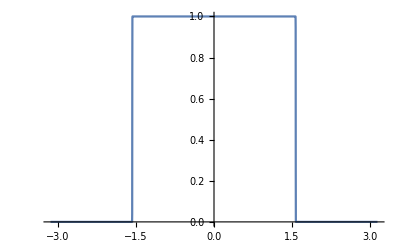

```mathematica
Plot[Theta[k],{k,-π,π}]
```

## KF

K_F in my notations defines an integration domain for gauss matrices, i.e.  θ(k)=1/(2+exp(-2cos(k)))  should determine K_F

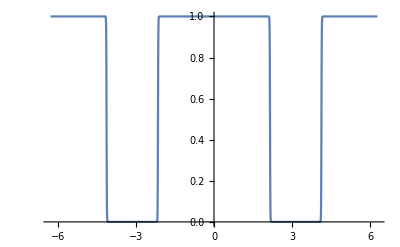

1.

```mathematica
B=-1.1;
β=100;
ϵ[k_]=-2Cos[k];
θ[k_]:=Exp[-β B]/(2Cosh[β B]+Exp[ϵ[k]*β]);
θ1[k_]:=1/(1+Exp[2β B]+Exp[(ϵ[k]+B)*β]);
Plot[{θ[k], θ1[k_]},{k,-2π,2π}]
θ[0.0]
```

```mathematica
1.
```

1.

```mathematica
θ[π/2]
θ1[0.]
```

1.

1.

```mathematica
Exp[ϵ[0.]*β]
```

1.3839×10^-87

```mathematica
r_plus_elem
```

## t=0 exact profile

Eq(46) in Abarenkova

```mathematica
<<NumericalDifferentialEquationAnalysis`
Distribution50:=N[GaussianQuadratureWeights[30,-π,π]];
θ[k_]=1.0/(2.0+Exp[-2Cos[k]100]);
ϵ=10^-8;
KernelV[x_,k_,q_]=-√θ[k] 1/(2π)(*If[k≠q,Sin[Abs[x](k-q)/2]/Tan[(k-q)/2],Abs[x]]*)Sin[Abs[x](k-q+ϵ)/2]/Tan[(k-q+ϵ)/2] √θ[q];
KernelR[x_,k_,q_]=KernelV[x,k,q]+√θ[k] Exp[-ⅈ x (k+q)/2] √θ[q];
MatrixV[x_]=IdentityMatrix[Length[(Distribution50)]]+Table[√((Distribution50)[[i]][[2]])*
KernelV[
x,(Distribution50)[[i]][[1]],(Distribution50)[[j]][[1]]
]*
√((Distribution50)[[j]][[2]]),{i,1,Length[(Distribution50)]},{j,1,Length[(Distribution50)]}];
MatrixR[x_]=IdentityMatrix[Length[(Distribution50)]]+Table[√((Distribution50)[[i]][[2]])*
KernelR[
x,(Distribution50)[[i]][[1]],(Distribution50)[[j]][[1]]
]*
√((Distribution50)[[j]][[2]]),{i,1,Length[(Distribution50)]},{j,1,Length[(Distribution50)]}];
Grep[x_]:=Det[MatrixR[x]]-Det[MatrixV[x]];
```

```mathematica
Greptable50=Table[{x,Grep[x]},{x,-10,10,1}];
```

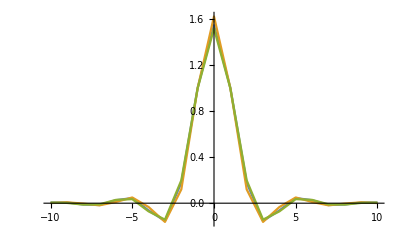

```mathematica
ListLinePlot[{Greptable30,Greptable40,Greptable50},PlotRange->All]
```

```mathematica
1-1/π NIntegrate[θ[k],{k,-π,π}]
1/(2π)NIntegrate[θ[k],{k,-π,π}]
```

0.498897

0.250552

General::munfl: 1. 2.12726786174656×10^-866 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

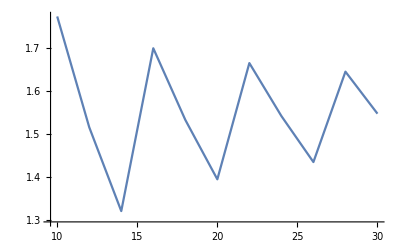

```mathematica
ListLinePlot[Table[{M,Grep[0,M]},{M,10,30,2}]]
```

```mathematica
Integrate[Exp[ⅈ x],{x,0,2π}]
```

0

## Grep for a single point

Eq(46) in Abarenkova

```mathematica
<<NumericalDifferentialEquationAnalysis`
Distribution50:=N[GaussianQuadratureWeights[30,-π/2,π/2]];
x=0;
t=0;
ϵ=10^-8;
γ=2;
θ[k_]=1.0/(2.0+Exp[-2Cos[k]1000]);
τ[k_]=-2t Cos[k]-x k;
EPV[k_]:=1/(2π)NIntegrate[(Exp[-ⅈ τ[q]]-Exp[-ⅈ τ[k]])/Tan[(q-k)/2],{q,-π,π}];
G=ⅈ^x BesselJ[x,2t];
Eminus[k_]=Exp[ⅈ/2 τ[k]];
Eplus[k_]:=EPV[k]*Eminus[k];
lplus[k_,η_]:=((1-Cos[η])/2 Eplus[k]+Sin[η]/2 1/Eminus[k])√θ[k];
lminus[k_]=Eminus[k] √θ[k];
F[η_]=3/(5-4 Cos[η]);

KernelNu[k_,q_,η_]:=(lplus[k+ϵ,η]*lminus[q]-lplus[q,η]*lminus[k+ϵ])/(2π Tan[(k+ϵ-q)/2]);
KernelRminus[k_,q_]=1/(2π)lminus[k]*lminus[q];
(*KernelRplus[k_,q_,η_]:=1/(π(1-Cos[η]))lplus[k,η]*lplus[q,η];*)
KernelRplus[k_,q_,η_]:=1/π((1-Cos[η])/4 Eplus[k]Eplus[q]+
Sin[η]/4(Eplus[k]/Eminus[q]+Eplus[q]/Eminus[k])+(1+Cos[η])/4 1/(Eminus[q]Eminus[k]))√θ[k] √θ[q];
KernelQ[k_,q_,η_]:=KernelNu[k,q,η]-(1-Cos[η])/2 G KernelRminus[k,q];
KernelQR[k_,q_,η_]:=γ KernelQ[k,q,η]-γ KernelRplus[k,q,η];
KernelSecond[k_,q_,η_]:=γ KernelQ[k,q,η];


MatrixQR[η_]:=IdentityMatrix[Length[(Distribution50)]]+Table[√((Distribution50)[[i]][[2]])*
KernelFirst[
(Distribution50)[[i]][[1]],(Distribution50)[[j]][[1]],η
]*
√((Distribution50)[[j]][[2]]),{i,1,Length[(Distribution50)]},{j,1,Length[(Distribution50)]}];
MatrixSecond[η_]:=IdentityMatrix[Length[(Distribution50)]]+Table[√((Distribution50)[[i]][[2]])*
KernelSecond[(Distribution50)[[i]][[1]],(Distribution50)[[j]][[1]],η
]*
√((Distribution50)[[j]][[2]]),{i,1,Length[(Distribution50)]},{j,1,Length[(Distribution50)]}];
```

```mathematica
Det[MatrixQR[1.]]
(G-1)Det[MatrixSecond[1.]]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

0.506472

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

0.

```mathematica
(*(G-1)Det[MatrixSecond[η]*)
```

```mathematica
1/(2π)NIntegrate[F[η](Det[MatrixQR[η]](*+(G-1)Det[MatrixSecond[η]]*)),{η,-π,π}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::munfl: 3.73305×10^-301 (-1.01521×10^-220) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.73305×10^-301 (-9.1459×10^-218) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.73305×10^-301 2.4877×10^-194 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.

```mathematica
1-γ/(2π)NIntegrate[θ[k],{k,-π,π}]
1/(2π)NIntegrate[θ[k],{k,-π,π}]
```

0.5

0.25

```mathematica
MatrixSecond//Chop//MatrixForm
MatrixQR//Chop//MatrixForm
MatrixRplus//Chop//MatrixForm
```

(1. | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0
0 | 0 | -0.515294+2.77339 ⅈ | -0.108584+0.198244 ⅈ | 0 | 0
0 | 0 | -0.108584+0.198244 ⅈ | 0.364259+1.16465 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 1.)

(1. | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0
0 | 0 | -0.395337+2.97416 ⅈ | -0.255444+0.379471 ⅈ | 0 | 0
0 | 0 | -0.255444+0.379471 ⅈ | 0.144146+1.0893 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 1.)

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -0.0408017-0.0682872 ⅈ | 0.0499525-0.0616422 ⅈ | 0 | 0
0 | 0 | 0.0499525-0.0616422 ⅈ | 0.0748686+0.0256309 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

## t → 0 for integral kernels

So, at the present moment we found a suspicious part in a Erf function at t → 0. 
Erf((x-qt)/(2 √t)(1+i))

General::munfl: Exp[-1544.04+244751. ⅈ] is too small to represent as a normalized machine number; precision may be lost.

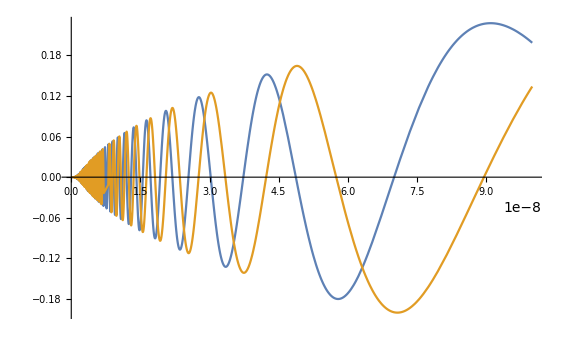

```mathematica
q=1.0;
f[x_,t_]=Erf[(x-q a t)/(2 √(a t))(-1+ⅈ)];
coor =+ 0.001Exp[+ⅈ π 0.001];
Plot[{Re[f[coor,t]]+1,-Im[f[coor,t]]},{t,0,0.0000001}]
```

```mathematica
Assuming[p<x&& x<0,Integrate[Exp[ⅈ q x]/(q-p),{q,-∞,∞}, PrincipalValue->True] ]
```

-ⅈ ⅇ^(ⅈ p x) π

## 2D

```mathematica
<<MaTeX`
A=Import["~/Programs/HardCoreBosons/Data/2D/data2d_fft_Gauss61.dat"];
A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<4&)];
A=A[[;;,{1,2,3}]]; (*x, t, Re[G(x,t), Im[G(x,t)]]*)
```

```mathematica
ListDensityPlot[A]
```

$Aborted

```mathematica
A=Table[1.0Sinc[√((x/10)^2+(y/10)^2)],{x,-100,100},{y,-100,100}];
ListDensityPlot[A,InterpolationOrder-> 3]
```

-Graphics-

## Λ and η

```mathematica
η[Λ_]=2ArcCot[-Λ];
Sin[η[Λ]/2]^2//Simplify
Sin[η[Λ]/2]Cos[η[Λ]/2]//Simplify
D[η[Λ],Λ]
```

1/(1+Λ^2)

-Λ/(1+Λ^2)

2/(1+Λ^2)

```mathematica
Cos[η[Λ]/2]
(-Λ/(1+Λ^2))/(√(1/(1+Λ^2)))
```

1/(√(1+1/Λ^2))

-Λ √(1/(1+Λ^2))

```mathematica
Λ[η_]=-Cot[η/2]
D[Λ[η],η]
```

-Cot[η/2]

1/2 Csc[η/2]^2

```mathematica
√(0.985748^2+0.032087^2)
```

0.98627

## Does Det[𝟙] = 1 ?

```mathematica
<<NumericalDifferentialEquationAnalysis`
Distribution50=N[GaussianQuadratureWeights[50,-1,1]];

IdentityMatrix[Length[Distribution50]]+Table[√(Distribution50[[i]][[2]])KroneckerDelta[i,j] √(Distribution50[[j]][[2]]),{i,1,Length[Distribution50]},{j,1,Length[Distribution50]}];
Det[%]
```

7.04837

## Vadims contour

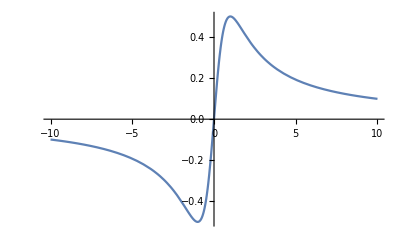

```mathematica
Plot[x/(1+x^2),{x,-10,10}]
```

```mathematica
z=x+ⅈ x/(1+x^2)
ⅆz ==
```

```mathematica
D[ⅈ x/(1+x^2),x]//Simplify
```

-(ⅈ (-1+x^2))/((1+x^2)^2)

```mathematica
0.923674 for vadims trick
0.923275 standart one
```

```mathematica
0.510277
```

## G(p=0,t)

So, in the C++ code I sum 
G(p=0,t) = ∫e^ipx G(x,t)ⅆx |_(p=0)=∫G(x,t ) ⅆx

```mathematica
<<MaTeX`
Data1M15=Import["~/Programs/HardCoreBosons/Data/Gp_contour/M15/1/Gxt_sum_15.dat"];
Data1M15=Drop[Data1M15,1];
Data1M15=DeleteCases[Data1M15,_?(Length[#]<2&)];
Data1M15=Data1M15[[;;,{1,2,3}]]; (*t, Re, Im*)

Data2M15=Import["~/Programs/HardCoreBosons/Data/Gp_contour/M15/2/Gxt_sum_15.dat"];
Data2M15=Drop[Data2M15,1];
Data2M15=DeleteCases[Data2M15,_?(Length[#]<2&)];
Data2M15=Data2M15[[;;,{1,2,3}]]; (*t, Re, Im*)

Data1M31=Import["~/Programs/HardCoreBosons/Data/Gp_contour/M31/1/Gxt_sum_31.dat"];
Data1M31=Drop[Data1M31,1];
Data1M31=DeleteCases[Data1M31,_?(Length[#]<2&)];
Data1M31=Data1M31[[;;,{1,2,3}]]; (*t, Re, Im*)

Data2M31=Import["~/Programs/HardCoreBosons/Data/Gp_contour/M31/2/Gxt_sum_31.dat"];
Data2M31=Drop[Data2M31,1];
Data2M31=DeleteCases[Data2M31,_?(Length[#]<2&)];
Data2M31=Data2M31[[;;,{1,2,3}]]; (*t, Re, Im*)


Sites=Data2M31[[;;,1]];
Sites=Union[Sites];
SystemSize =Length[Sites]; 
xmin=1;
xmax=SystemSize-1;(* cause Subscript[σ^z, l+1] can ∃ l < SystemSize-1 *)
SHIFT=1.5; (*To match 0 in data with 0 on the plot*)

radius=5;
widht=Thickness[0.2];
CircleEdgeWidht=Thickness[0.009];
CROSSd ={AbsoluteThickness[radius/8],Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]};
CROSS ={AbsoluteThickness[radius/8],Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]};
DIAMOND = Polygon[{{1,0},{0,1},{-1,0},{0,-1}}];

RED0=Graphics[{EdgeForm[CircleEdgeWidht],RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,DIAMOND}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];
BLACK=Graphics[{RGBColor[0,0,0],Disk[]}];
SciPostYellow = Graphics[{RGBColor[246/255,161/255,26/255],Disk[]}];
SciPostBlue = Graphics[{RGBColor[104/255,133/255,195/255],Disk[]}];
```

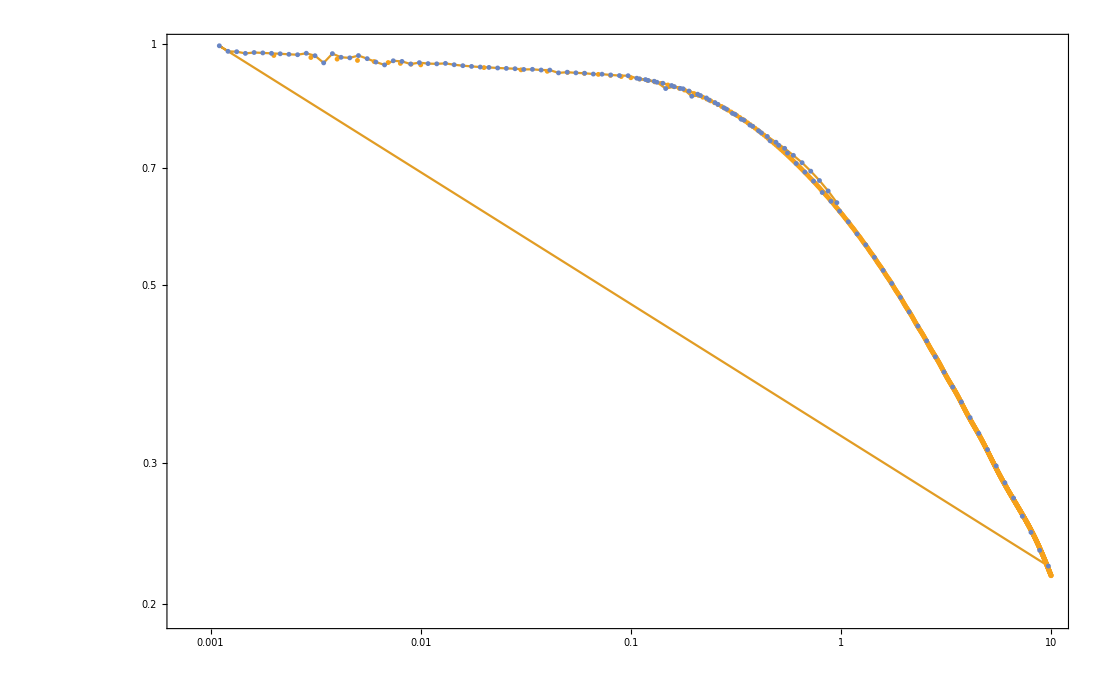

```mathematica
FIG=ListLogLogPlot[{
Join[Table[{Data1M15[[n,1]],√(Data1M15[[n,2]]^2+Data1M15[[n,3]]^2)},{n,1,Length[Data1M15]}]
,Table[{Data2M15[[n,1]],√(Data2M15[[n,2]]^2+Data2M15[[n,3]]^2)},{n,1,Length[Data2M15]}]
]
,Join[Table[{Data1M31[[n,1]],√(Data1M31[[n,2]]^2+Data1M31[[n,3]]^2)},{n,1,Length[Data1M31]}]
,Table[{Data2M31[[n,1]],√(Data2M31[[n,2]]^2+Data2M31[[n,3]]^2)},{n,1,Length[Data2M31]}]
]

},
Joined->{False,True}
,Frame->True
,FrameStyle->BlackFrame
,Axes->{True,False}
,BaseStyle->{FontFamily->"Latin Modern Roman"}
,FrameLabel->MaTeX[{"t","G(p=0,t)"},FontSize->30]
,LabelStyle->Directive[FontSize->20]
,LABELS={
"\\rm GaussM = 15"
,"\\rm GaussM = 31"
(*,"\\sigma^x(t="<>ToString[TimeSlice1]<>")"*)

};
PlotLegends->Placed[MaTeX[LABELS,FontSize -> 20],{0.5,0.4}]
,PlotRange->{{Automatic,Automatic},{Automatic,Automatic}}
,PlotMarkers->{
{SciPostYellow, radius},
{SciPostBlue,radius}
}
 ]
```

```mathematica
Join[Table[{Data1M31[[n,1]],√(Data1M31[[n,2]]^2+Data1M31[[n,3]]^2)},{n,1,Length[Data1M31]}]
,Table[{Data2M31[[n,1]],√(Data2M31[[n,2]]^2+Data2M31[[n,3]]^2)},{n,1,Length[Data2M31]}]
]
```

{}

## Notes

Should determinant be equal to 1 ??? I think not,
But  ∫G(x,t=0) ⅆx ==1 ? In fact No, but |∫ G(x,t) | == 1

Compare with Sashas’ previous results. Done
Apply Vadims’ idea of the changed contour.


I have to report that Sashas formula has additional amplitude dependency on the coordinate x

## G(x,t) for a given X and T

```mathematica
β=100.0;
m=1.0;
μ=0.5*(π *0.5)^2/m;
x=1.7;
t=1.0;
G0=Exp[(-ⅈ π)/4] √(m/(2π t))Exp[ⅈ(m x^2)/(2t)];
Energy[p_]=p^2/(2.0m);
τ[p_]=t*Energy[p]-x*p;
PV[p_]=ⅈ π Exp[-ⅈ τ[p]]*Erf[(x-p*t)(1-ⅈ)/(2 √t)];
θ[p_]=1.0/(Exp[β(Energy[p]-μ)]+1);
Eminus[p_]=√(θ[p]/π)Exp[ⅈ τ[p]/2];
Einf[p_,η_]=Sin[η/2]*Sin[η/2] 1/π PV[p]+Sin[η/2]Cos[η/2]Exp[-ⅈ τ[p]];
EinfW[p_,η_]=Sin[η/2] 1/π PV[p]+Cos[η/2]Exp[-ⅈ τ[p]];
Eplus[p_,η_]=Eminus[p]*Einf[p,η];
ϵ=10^-6;
V[p_,q_,η_]=(Eplus[p+ϵ,η]*Eminus[q]-Eplus[q,η]*Eminus[p+ϵ])/(p+ϵ-q);
W[p_,q_,η_]=1/2.0 Eminus[p]*EinfW[p,η]*Eminus[q]*EinfW[q,η];

<<NumericalDifferentialEquationAnalysis`
Distr=N[GaussianQuadratureWeights[20,-π/2,π/2]];
Matrix1[η_]:=IdentityMatrix[Length[Distr]]+Table[√(Distr⟦i⟧⟦2⟧)V[Distr⟦i⟧⟦1⟧,Distr⟦j⟧⟦1⟧,η] √(Distr[[j]][[2]]),{i,1,Length[Distr]},{j,1,Length[Distr]}];
Matrix2[η_]:=IdentityMatrix[Length[Distr]]+Table[√(Distr⟦i⟧⟦2⟧)(V[Distr⟦i⟧⟦1⟧,Distr⟦j⟧⟦1⟧,η]-W[Distr⟦i⟧⟦1⟧,Distr⟦j⟧⟦1⟧,η])√(Distr⟦j⟧⟦2⟧),{i,1,Length[Distr]},{j,1,Length[Distr]}];
Det[Matrix1[1.0]]
Det[Matrix2[1.0]]
Grepeta[η_]:=(G0-1)Det[Matrix1[η]]+Det[Matrix2[η]];

(*Matrix1//MatrixForm//Chop
Matrix2//MatrixForm//Chop*)
```

0.599169+0.627103 ⅈ

0.523839+0.475147 ⅈ

```mathematica
δη=0.001;
G=ParallelSum[Grepeta[η]δη,{η,-π,π,δη}]/(2π)//Timing
```

{13.5349,0.0714873-0.0569888 ⅈ}

```mathematica
Distr2=N[GaussianQuadratureWeights[16,-π,π]];
ParallelSum[Grepeta[Distr2⟦i⟧⟦1⟧]*Distr2[[i]][[2]],{i,1,Length[Distr2]}]/(2π)//Timing
```

{0.062803,0.0717448-0.0569094 ⅈ}

0.0713951-0.0573193 ⅈ

```mathematica
Grepeta[0.1]
```

0.168455+0.189074 ⅈ

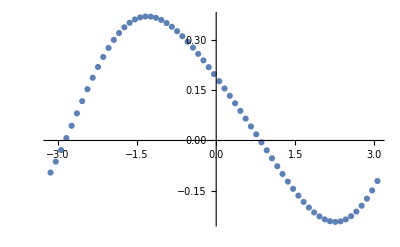

```mathematica
ListPlot[Table[{η,Re[Grepeta[η]]},{η,-π,π,0.1}]]
```

```mathematica
k=1.5;
G0[x,t]
τ[k]
PV[k]
θ[k]
Eminus[k]
Einf[k]
Eplus[k]
```

(0.315259+0.244473 ⅈ)[1.7,1.]

-1.425

-0.301899+0.400219 ⅈ

0.999981

0.426935-0.368823 ⅈ

Einf[1.5]

Eplus[1.5]

## Compiled G(x,t) for a given X and T

```mathematica
<<CompiledFunctionTools`
β=100.0;
m=1.0;
μ=0.5*(π *0.5)^2/m;
x=5.0;
t=10.0;
G0=Exp[(-ⅈ π)/4] √(m/(2π t))Exp[ⅈ(m x^2)/(2t)];
CEnergy=Compile[{{p,_Complex}},(p*p)/2.0];
Cτ=Compile[{{p,_Complex},{coord,_Complex},{time,_Complex}},time*CEnergy[p]-coord*p];
Cθ=Compile[{{p, _Complex},{beta, _Complex},{mu, _Complex}},1.0/(Exp[beta(CEnergy[p]-mu)]+1)];
CEminus=Compile[{{p, _Complex}},√(Cθ[p,β,μ]/π)Exp[ⅈ Cτ[p,x,t]/2]];
```

```mathematica
Do[θ[1.0,β,μ],{10^6}]//RepeatedTiming
Do[Cθ[1.0,β,μ],{10^6}]//RepeatedTiming
```

{0.232,Null}

{0.5412,Null}

```mathematica
FErf[p_,coord_,time_]=Erf[(coord-p*time)(0.5(1.0-ⅈ))/Sqrt[time]];
CErf=Compile[{{p,_Complex},{coord,_Complex},{time,_Complex}},FErf[p,coord,time]]
```

CompiledFunction[…]

```mathematica
Do[FErf[1.0,x,t],{10^5}]//RepeatedTiming
Do[CErf[1.0,x,t],{10^5}]//RepeatedTiming
```

{2.31,Null}

{2.45,Null}

```mathematica
Fsqrt[p_]=Sqrt[p];
Csqrt=Compile[{{p,_Real}},Sqrt[p]]
```

CompiledFunction[…]

```mathematica
Do[Sqrt[0.5],{10^6}]//RepeatedTiming
Do[Csqrt[0.5],{10^6}]//RepeatedTiming
```

{0.13,Null}

{0.272,Null}

```mathematica
Clear[CEminus,Cτ, Cθ]
```

```mathematica
CErf[p_]=Erf[(x-p*t)((*√2 Exp[-ⅈ π/4.0]*)(1.0-ⅈ))/(2.0Sqrt[t])];
(*CErf=Compile[{{p,_Complex}},2/(√π)NIntegrate[Exp[-z*z],{z,0,(x-p*t)((*√2 Exp[-ⅈ π/4.0]*)(1.0-ⅈ))/(2.0Sqrt[t])}]];*)
(*CompilePrint[CErf];*)
CErf[1.7]
CPV=Compile[{{p,_Complex}},ⅈ π Exp[-ⅈ Cτ[p]]*CErf[p]];
(*CompilePrint[CPV];*)
CPV[1.7]
```

-1.01357+0.207604 ⅈ

CompiledFunction::cfct: Number of arguments 1 does not match the length 3 of the argument template.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfct: Number of arguments 1 does not match the length 3 of the argument template.

(-0.652206-3.18422 ⅈ) ⅇ^(-ⅈ CompiledFunction[…][1.7])

```mathematica
CW[0.2,-1.0,0.0]
```

-0.0178496+0.158151 ⅈ

```mathematica
CEinf=Compile[{{p, _Complex},{η, _Complex}},Sin[0.5*η]*Sin[0.5*η] 1/π CPV[p]+Sin[0.5*η]Cos[0.5*η]Exp[-ⅈ Cτ[p]]];
CEinfW=Compile[{{p, _Complex},{η, _Complex}},Sin[0.5*η] 1/π CPV[p]+Cos[0.5*η]Exp[-ⅈ Cτ[p]]];
CEplus=Compile[{{p, _Complex},{η, _Complex}},CEminus[p]*CEinf[p,η]];
ϵ=10^-6;
CV=Compile[{{p,_Complex},{q,_Complex},{η,_Complex}},(CEplus[p+ϵ,η]*CEminus[q]-CEplus[q,η]*CEminus[p+ϵ])/(p+ϵ-q)];
CW=Compile[{{p,_Complex},{q,_Complex},{η,_Complex}},1/2.0 CEminus[p]*CEinfW[p,η]*CEminus[q]*CEinfW[q,η]];
```

```mathematica
<<NumericalDifferentialEquationAnalysis`
Distr=N[GaussianQuadratureWeights[8,-π/2,π/2]];

Matrix1=Function[{{η,_Complex}},Table[KroneckerDelta[i,j]+√(Distr⟦i⟧⟦2⟧)CV[Distr⟦i⟧⟦1⟧,Distr⟦j⟧⟦1⟧,η] √(Distr[[j]][[2]]),{i,1,Length[Distr]},{j,1,Length[Distr]}]] ;
CMatrix1=FunctionCompile[Matrix1[η],CompilerOptions->{"AbortHandling"->False}]
```

Function::flpar: Parameter specification {{η,_Complex}} in Function[{{η,_Complex}},Table[i+√(Distr⟦i⟧⟦2⟧) CV[Distr⟦i⟧⟦1⟧,Distr⟦j⟧⟦1⟧,η] √(Distr⟦j⟧⟦2⟧),{i,1,Length[Distr]},{j,1,Length[Distr]}]] should be a symbol or a list of symbols.

FunctionCompile::fun: Argument Function[{{η,_Complex}},Table[i+√(Distr⟦i⟧⟦2⟧) CV[Distr⟦i⟧⟦1⟧,Distr⟦j⟧⟦1⟧,η] √(Distr⟦j⟧⟦2⟧),{i,1,Length[Distr]},{j,1,Length[Distr]}]][η] is expected to be a Function.

FunctionCompile[Function[{{η,_Complex}},Table[i,j+√(Distr⟦i⟧⟦2⟧) CV[Distr⟦i⟧⟦1⟧,Distr⟦j⟧⟦1⟧,η] √(Distr⟦j⟧⟦2⟧),{i,1,Length[Distr]},{j,1,Length[Distr]}]][η],CompilerOptions→{AbortHandling→False}]

```mathematica
CMatrix1[1.0]
```

FunctionCompile[Function[{{η,_Complex}},Table[i,j+√(Distr⟦i⟧⟦2⟧) CV[Distr⟦i⟧⟦1⟧,Distr⟦j⟧⟦1⟧,η] √(Distr⟦j⟧⟦2⟧),{i,1,Length[Distr]},{j,1,Length[Distr]}]][η],CompilerOptions→{AbortHandling→False}][1.]

```mathematica
Det[CMatrix1[1.0]]
```

Det[Missing[NotAvailable,1.]]

```mathematica
CMatrix1[η_]:=Table[KroneckerDelta[i,j]+√(Distr⟦i⟧⟦2⟧)CV[Distr⟦i⟧⟦1⟧,Distr⟦j⟧⟦1⟧,η] √(Distr[[j]][[2]]),{i,1,Length[Distr]},{j,1,Length[Distr]}];
CMatrix2[η_]:=Table[KroneckerDelta[i,j]+√(Distr⟦i⟧⟦2⟧)(CV[Distr⟦i⟧⟦1⟧,Distr⟦j⟧⟦1⟧,η]-CW[Distr⟦i⟧⟦1⟧,Distr⟦j⟧⟦1⟧,η])√(Distr⟦j⟧⟦2⟧),{i,1,Length[Distr]},{j,1,Length[Distr]}];
Det[CMatrix1[1.0]]
Det[CMatrix2[1.0]]
CGrepeta[η_]:=(G0-1)Det[CMatrix1[η]]+Det[CMatrix2[η]];
G=NIntegrate[CGrepeta[η],{η,-π,π}]/(2π)
(*Matrix1//MatrixForm//Chop
Matrix2//MatrixForm//Chop*)
```

CompiledFunction::cfse: Compiled expression -0.270033-0.0126519 ⅈ should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression -0.270033-0.0126519 ⅈ should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression -0.270033-0.0126519 ⅈ should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfse will be suppressed during this calculation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

-0.567237+0.503413 ⅈ

-0.44968+0.482989 ⅈ

CompiledFunction::cfsa: Argument η at position 2 should be a machine-size complex number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.+0. ⅈ

```mathematica
CW[0.2,-1.0,0.0]//Timing
W[0.2,-1.0,0.0]//Timing
```

{0.001027,-0.0178496+0.158151 ⅈ}

{0.000658,-0.0178496+0.158151 ⅈ}

```mathematica
A=Table[{η,Re[Grepeta[η]]},{η,-π,π,0.1}]//Timing
```

{9.98889,{{-3.14159,0.0829346},{-3.04159,0.0925504},{-2.94159,0.0961193},{-2.84159,0.0934318},{-2.74159,0.0847907},{-2.64159,0.0709681},{-2.54159,0.0531194},{-2.44159,0.0326659},{-2.34159,0.011159},{-2.24159,-0.00985927},{-2.14159,-0.0289851},{-2.04159,-0.0450594},{-1.94159,-0.0572432},{-1.84159,-0.0650585},{-1.74159,-0.0683927},{-1.64159,-0.0674715},{-1.54159,-0.0628056},{-1.44159,-0.0551196},{-1.34159,-0.045272},{-1.24159,-0.0341748},{-1.14159,-0.0227189},{-1.04159,-0.0117121},{-0.941593,-0.00183102},{-0.841593,0.00641055},{-0.741593,0.0126785},{-0.641593,0.0168218},{-0.541593,0.0188644},{-0.441593,0.0189888},{-0.341593,0.0175123},{-0.241593,0.014858},{-0.141593,0.0115202},{-0.0415927,0.00802673},{0.0584073,0.00489653},{0.158407,0.00259587},{0.258407,0.00149405},{0.358407,0.00182249},{0.458407,0.00364122},{0.558407,0.00681748},{0.658407,0.0110212},{0.758407,0.0157408},{0.858407,0.0203211},{0.958407,0.0240229},{1.05841,0.0261003},{1.15841,0.0258889},{1.25841,0.0228954},{1.35841,0.0168793},{1.45841,0.00791283},{1.55841,-0.00358788},{1.65841,-0.0168694},{1.75841,-0.0308875},{1.85841,-0.0443914},{1.95841,-0.0560403},{2.05841,-0.0645383},{2.15841,-0.068776},{2.25841,-0.06796},{2.35841,-0.0617161},{2.45841,-0.0501527},{2.55841,-0.0338748},{2.65841,-0.0139464},{2.75841,0.00819665},{2.85841,0.0308741},{2.95841,0.0523161},{3.05841,0.0708285}}}

```mathematica
CA=Table[{η,Re[CGrepeta[η]]},{η,-π,π,0.1}]//Timing
```

{11.2574,{{-3.14159,0.0829346},{-3.04159,0.0925504},{-2.94159,0.0961193},{-2.84159,0.0934318},{-2.74159,0.0847907},{-2.64159,0.0709681},{-2.54159,0.0531194},{-2.44159,0.0326659},{-2.34159,0.011159},{-2.24159,-0.00985927},{-2.14159,-0.0289851},{-2.04159,-0.0450594},{-1.94159,-0.0572432},{-1.84159,-0.0650585},{-1.74159,-0.0683927},{-1.64159,-0.0674715},{-1.54159,-0.0628056},{-1.44159,-0.0551196},{-1.34159,-0.045272},{-1.24159,-0.0341748},{-1.14159,-0.0227189},{-1.04159,-0.0117121},{-0.941593,-0.00183102},{-0.841593,0.00641055},{-0.741593,0.0126785},{-0.641593,0.0168218},{-0.541593,0.0188644},{-0.441593,0.0189888},{-0.341593,0.0175123},{-0.241593,0.014858},{-0.141593,0.0115202},{-0.0415927,0.00802673},{0.0584073,0.00489653},{0.158407,0.00259587},{0.258407,0.00149405},{0.358407,0.00182249},{0.458407,0.00364122},{0.558407,0.00681748},{0.658407,0.0110212},{0.758407,0.0157408},{0.858407,0.0203211},{0.958407,0.0240229},{1.05841,0.0261003},{1.15841,0.0258889},{1.25841,0.0228954},{1.35841,0.0168793},{1.45841,0.00791283},{1.55841,-0.00358788},{1.65841,-0.0168694},{1.75841,-0.0308875},{1.85841,-0.0443914},{1.95841,-0.0560403},{2.05841,-0.0645383},{2.15841,-0.068776},{2.25841,-0.06796},{2.35841,-0.0617161},{2.45841,-0.0501527},{2.55841,-0.0338748},{2.65841,-0.0139464},{2.75841,0.00819665},{2.85841,0.0308741},{2.95841,0.0523161},{3.05841,0.0708285}}}

```mathematica
2*4
```

```mathematica
(2.1+2.1+2+2)*2
```

16.4

```mathematica
%*4
```

65.6

```mathematica
(2.1+1.0+2.1+1.0)*2
```

12.4

```mathematica
78*170
```

13260

# Some stuff

```mathematica
f/@{1,2,3,4}
```

{f[1],f[2],f[3],f[4]}

```mathematica
f@@{1,2,3,4}
```

f[1,2,3,4]

```mathematica
g := #^2&
g[5]
```

25

```mathematica
#^2&[2]
```

4

```mathematica
f[2]
```

4

```mathematica
(#^2+#^2)&[2]
```

8

```mathematica
Erf[1.-ⅈ]
```

1.31615-0.190453 ⅈ